## Глава 2. Представление рядов в системах компьютерной математики.

## §1. Числовые ряды

### 1.1. Сходимость ряда. Абсолютная и условная сходимость. Признаки абсолютной сходимости.

Пусть имеется числовой ряд:

u_1+u_2+...+u_n+...=∑_(n=1)^∞ u_n

К р и т е р и й  К о ш и. Для того чтобы числовой ряд (1) был сходящимся, необходимо и достаточно, чтобы для любого ϵ>0 , существовало N=N(ϵ) такое, что для всех n>N и p=1,2.... выполнялось неравенство

|S_(n+p)-S_n|=|u_(n+1)+u_(n+2)+...+u_(n+p)|<ϵ

Н е о б х о д и м ы й  п р и з н а к   с х о д и м о с т и.  Если ряд (1) сходится, то

lim_(n→∞) u_n=0

Ряд (1) называется абсолютно сходящимся, если сходится ряд из модулей членов этого ряда, т.е. сходится ряд

|u_1|+|u_2|+...+|u_n|+...=∑_(n=1)^∞ |u_n|

Если ряд (1) сходится, а ряд (3) расходится, то ряд (1) называется условно сходящимся.

П р и з н а к  с р а в н е н и я  р я д о в. Если члены ряда (1) для всех n>N_0 удовлетворяют условию |u_n|≤ b_n, причем ряд ∑_(n=1)^∞ b_n  сходится, то ряд (1) сходится абсолютно. Если же для n>N_1 члены ряда (1) удовлетворяют условию 0≤ c_n≤ |u_n|, причем ряд ∑_(n=1)^∞ с_n расходится, то ряд (1) не сходится абсолютно.

П р е д е л ь н ы й  п р и з н а к  с р а в н е н и я.  Если ряд ∑_(n=1)^∞ b_n  сходится абсолютно и существует конечный предел lim_(n→∞) |u_n/b_n|=q<+∞, то ряд (1) также сходится абсолютно. Если же члены рядов u_n и b_n - действительные положительные числа и

0<lim_(n→∞) u_n/b_n<+∞

то ряды ∑_(n=1)^∞ u_n и  ∑_(n=1)^∞ b_n либо оба сходятся, либо оба расходятся.

П р и з н а к  Д а л а м б е р а. Если члены ряда (1) таковы, что существует конечный предел

lim_(n→∞) |(u_(n+1))/u_n|=q

то при 0≤ q<1 ряд (1) сходится абсолютно, при q>1 - расходится, а при q=1 требуется дополнительное исследование.

П р и з н а к  К о ш и. Пусть

lim_(n→∞) (|u_n|)^(1/n)=q

Тогда при 0≤ q<1 ряд (1) сходится абсолютно, при q>1  (1) - расходится, а при q=1 требуется дополнительное исследование .

И н т е г р а л ь н ы й  п р и з н а к  К о ш и. Пусть функция f(x) положительна и монотонна при x≥ 1, и пусть для всех n∈ℕ имеет равенство f(n)=|u_n|. Тогда числовой ряд (3) сходится абсолютно или расходится с несобственным интегралом:

∫_a^∞ f(x)ⅆx, a≥ 1

##### Пример №12.24

Используя признак сравнения или предельный признак сравнения, исследовать на сходимость следующий ряд:

∑_(n=1)^∞ (n^2+3)/(4 n^3+5n)

Так как ряд ∑1/n расходится, и:

```mathematica
Limit[(n^2+3)/(4 n^3+5n)/(1/n), n-> Infinity]
```

1/4

Значит, по предельному признаку сравнения исходный ряд также расходится.

##### Пример №12.33

Пользуясь признаком Даламбера, исследовать на сходимость следующий ряд:

3/1+(3·5)/(1·4)+...+(3·5·...(2n+1))/(1·4·...(3n-2))

Запишем n-ый член ряда с помощью функции Product[f,{i,i_max}], которая в традиционном виде выглядит как: ∏_(i=1)^i_max f(i)

```mathematica
u[n_]:=Product[2k+1,{k,n}]/Product[3k-2,{k,n}]
```

Для определения абсолютной сходимости ряда воспользуемся признаком Даламбера (4):

```mathematica
Limit[Abs[u[n+1]/u[n]],n-> Infinity]//N
```

0.666667

Так как 0≤ 0.67< 1, то данный ряд сходится.

##### Пример №12.45

Используя признак Коши, исследовать на сходимость следующий ряд:

∑_(n=1)^∞ n (arcsin 1/n)^n

Запишем член ряда:

```mathematica
u[n_]:=n ( ArcSin[1/n])^n
```

Воспользуемся признаком Коши (5):

```mathematica
Limit[ (n ArcSin[1/n]^n)^(1/n),n-> Infinity]
```

0

По признаку Коши ряд сходится.

##### Пример № 12.52

Используя интегральный признак Коши, исследовать на сходимость следующие ряды:

∑_(n=3)^∞ 1/(n ln n (ln ln n)^2)

Запишем член ряда:

```mathematica
u[n_]:= (n Log[n] ( Log[Log[n]] )^2 )^-1
```

Воспользуемся интегральным признаком Коши (6):

```mathematica
Integrate[u[x],{x,3,Infinity}]
```

1/Log[Log[3]]

Получили, что данный интеграл сходится, значит и исходный ряд также сходится.

Система Wolfram Mathematica имеет встроенную функцию проверки сходимости ряда: SumConvergence[f,n]. Продемонстрируем его работу:

```mathematica
SumConvergence[1/n,n]
```

False

```mathematica
SumConvergence[1/(n Log[n] Log[Log[n]]^3),n]
```

```mathematica
True
```

```mathematica
SumConvergence[(2^(n^2))/(n!),n]
```

False

```mathematica
SumConvergence[1/(√n)Log[(n+1)/(n-1)],n]
```

True

В методических целях будем применять критерии сходимости, изложенные в теоретической части, а использовать функцию SumConvergence[f,n] будем для самопроверки.

Задания под номерами №№12.19-12.86 рекомендуются к самостоятельному решению.

### 1.2. Признаки условной сходимости.

П р и з н а к  Л е й б н и ц а. Пусть члены a_n знакочередующегося ряда

a_1-a_2+a_3+...+(-1)^(n+1)a_n+...

действительны и монотонно убывают, т.е.

a_1>a_2>a_3>....>a_n

и

lim_(n→∞) a_n=0

Тогда ряд (7) сходится, причем для его суммы S имеет место оценка S<a_1

П р и з н а к  А б е л я - Д и р и х л е. Пусть члены последовательности (b_n) монотонно убывают: b_1>b_2>b_3...>b_n,  и lim_(n→∞) b_n=0, а частичные суммы S_n=a_1+a_2+...+a_n, ограничены в совокупности, т.е.

|∑_(k=1)^n a_k|≤ M

тогда ряд ∑_(n=1)^∞ a_n b_n сходится.

##### Пример №12.95

Исследовать на абсолютную и условную сходимость следующий ряд:

∑_(n=2)^∞ (-1)^n(ln n)/n

Запишем член ряда:

```mathematica
a[n_]:=(-1)^n Log[n]/n
```

Исследуем на абсолютную сходимость ряд при помощи интегрального признака Коши:

```mathematica
Integrate[Abs[a[x]],{x,2,Infinity}]
```

Integrate::idiv: Integral of Log[x]/x does not converge on {2,∞}.

∫_2^∞ ⅇ^(-π Im[x]) Abs[Log[x]/x]ⅆx

Получили сообщение о том, что интеграл расходится.

Так как ряд не сходится абсолютно, исследуем на условную сходимость по признаку Лейбница.

Покажем графически, что модули членов ряда убывают:

```mathematica
ListPlot[Table[Abs[a[n]],{n,3,10}]]
```

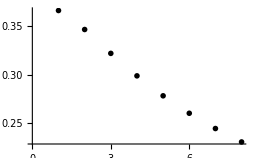

Первое условие признака Лейбница выполняется.

Найдем предел:

```mathematica
Limit[Abs[a[n]],n-> Infinity]
```

0

Условия признака Лейбница выполняются, следовательно ряд сходится условно. Проверим результат:

```mathematica
SumConvergence[Abs[a[n]],n]
```

False

```mathematica
SumConvergence[a[n],n]
```

True

Ответ: ряд сходится условно.

Данный порядок действий следует применить для решения задач под номерами №№12.90-12.109

## §2. Функциональные ряды

### 2.1. Область сходимости функционального ряда

Пусть функции f_n(z), n∈ℕ, определены в области D. Выражение

f_1(z)+f_2(z)+...+f_n(z)+...=∑_(n=1)^∞ f_n(z), z∈D

называется функциональным рядом. Если для z_0∈D, числовой ряд ∑_(n=1)^∞ f_n(z_0) сходится, то говорим, что функциональный ряд (1) сходится в точке z_0. Если в каждой точке z∈D_1⊂D числовые ряды ∑_(n=1)^∞ f_n(z) сходятся, то ряд (1) называется сходящимся в области D_1.

К р и т е р и й  К о ш и. Для того чтобы функциональный ряд (1) был сходящимся в области D_1, необходимо и достаточно, чтобы для любого ϵ>0 и для любого z_0∈D_1, существовало N=N(ϵ, z), такое, что

|f_(n+1)(z)+f_(n+2)(z)+...+f_(n+p)(z)|<ϵ, для всех n>N(ϵ,z) и p∈ℕ.

Для определения области абсолютной сходимости функционального ряда (1) следует воспользоваться либо признаком Даламбера, либо признаком Коши. Именно, если:

lim_(n→∞) |(f_(n+1)(z))/(f_n(z))|=q(z)   или

lim_(n→∞) (|f_n(z)|)^(1/n)=q(z) ,

то для определения области абсолютной сходимости ряда (1) следует решить функциональное неравенство q(z)<1. При этом для изучения поведения ряда в граничных точках получаемой области, т.е. в точках, описываемых уравнением q(z)=1, требуется дополнительное исследование.

##### Пример №12.124

Найти область сходимости ряда (x∈ℝ). Исследовать ряд на абсолютную сходимость.

∑_(n=1)^∞ (-1)^n n^-x

Запишем общий член ряда:

```mathematica
f[n_,x_]:=(-1)^n n^-x
```

По признаку Лейбница данный ряд сходится при любых x| x>0, так как выполняются все необходимые условия.

На границе сходимости x=0 получим ряд:

∑_(n=1)^∞ (-1)^n

Данный ряд не является сходящимся, и следовательно область сходимости исходного ряда: x>0

Ряд, составленный из модулей будет выглядеть так:

∑_(n=1)^∞ 1/n^x

Данный ряд сходится абсолютно при x>1. Докажем это, используя интегральный признак Коши:

```mathematica
Integrate[1/n^x,{n,1,Infinity},Assumptions->x∈Reals]
```

ConditionalExpression[1/(-1+x),x>1]

Получили, что x >1. Следовательно, область сходимости данного ряда:  x∈(1,+∞).

##### Пример №12.125

Найти область сходимости ряда (x∈ℝ). Исследовать ряд на абсолютную сходимость.

∑_(n=1)^∞ (cos(n x))/(n √n)

Запишем член ряда:

```mathematica
f[n_,x_]:=Cos[n x]/n^(3/2)
```

Чтобы воспользоваться признаком Абеля-Дирихле необходимо доказать, что частичные суммы ряда ∑_(k=1)^n Cos(n x) ограничены в совокупности:

```mathematica
Sum[Cos[k x],{k,1,n}]
```

Cos[1/2 (1+n) x] Csc[x/2] Sin[(n x)/2]

Так как произведение Sin(a)Cos(b) по модулю не превосходит 1 при любых а и b, имеем:

|∑_(n=1)^∞ cos(n x)|≤ 1/(|sin(x/2)|)      x≠ 0

Что и требовалось доказать.

Так как ряд ∑_(n=1)^∞ 1/n^(3/2) сходится, то и исходный ряд:

∑_(n=1)^∞ (cos(n x))/(n √n)

по признаку Абеля-Дирихле сходится при любых x≠0. Следовательно область сходимости данного ряда: x ∈ℝ \ {0}

##### Пример №12.136

Найти область абсолютной сходимости ряда:

∑_(n=1)^∞ (n 2^n)/(z-3ⅈ)^(2n)

Запишем общий член ряда:

```mathematica
f[n_,z_]:=(n 2^n)/(z-3I)^(2n)
```

Найдем область сходимости данного ряда по признаку Даламбера:

```mathematica
Limit[f[n+1,z]/f[n,z],n->Infinity]
```

2/(-3 ⅈ+z)^2

Получили, что исходный ряд сходится в кольце:

2/(|-3 ⅈ+z|^2)<1
|z-3ⅈ|^2>2
|z-3ⅈ| >√2

На границе области получаем следующий ряд:

∑_(n=1)^∞ (n 2^n)/(√2)^(2n)=∑_(n=1)^∞ n

Так как ряд на границе не сходится,  то областью сходимости исходного ряда будет: |z-3ⅈ| >√2

##### Пример №12.138

Найти область абсолютной сходимости:

∑_(n=1)^∞ 1/n^2 ⅇ^(-n z^2)

Запишем общий член ряда:

```mathematica
f[n_,z_]:=1/n^2 Exp[-n z^2]
```

Для того чтобы определить область сходимости, воспользуемся признаком Коши:

```mathematica
Limit[f[n,z]^(1/n),n-> Infinity]
```

ⅇ^(-z^2)

Получаем условие:e^(-z^2)<1 ⇒ Re[z^2]≥ 0.

Из алгебраической формы записи z=x+I y, z^2=x^2-y^2+2I x y следует, что x^2-y^2≥ 0

Изобразим решение данного неравенства:

```mathematica
RegionPlot[x^2-y^2≥ 0,{x,-3,3},{y,-3,3},Axes->True,Frame->False]
```

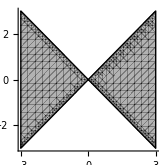

Из графика видно, что ряд сходится в: D={z| -π/4 ≤ arg(z)≤ π/4&& 3π/4≤ arg(z)≤ 5π/4}

С использованием описанных выше методов рекомендуется решить задания №№12.124-12.143.

### 2.2. Равномерная сходимость

Сходящийся в области D_1 функциональный ряд (1) называется равномерно сходящимся в этой области, если для любого ϵ>0 найдется N=N(ϵ) такое, что для остатка ряда (1)

R_n(z)=∑_(k=n+1)^∞ f_k(z)

при всех n>N(ϵ) и z∈D_1 имеет место оценка:

|R_n(z)|<ϵ

К р и т е р и й  К о ш и  р а в н о м е р н о й  с х о д и м о с т и. Для того чтобы функциональный ряд (1) был равномерно сходящимся в области D_1, необходимо и достаточно, чтобы для любого ϵ>0 существовало N=N(ϵ) такое, что для всех n>N(ϵ) и z∈D_1 выполнялись неравенства

|f_(n+1)(z)+f_(n+2)(z)+...+f_(n+p)(z)|<ϵ, p=1,2...

П р и з н а к  В е й е р ш т р а с с а. Пусть функциональный ряд (1) сходится в области D_1, и пусть существует сходящийся знакоположительный числовой ряд ∑_(n=1)^∞ a_n, такой, что для всех n>N_0 и z∈D_1 члены ряда (1) удовлетворяют условию:

|f_n(z)|≤ a_n

Тогда ряд (1) сходится абсолютно и равномерно в области D_1.

##### Пример №1

Исследовать функциональный ряд:

∑_(n=2)^∞ (2^n(z+3)^n)/(n (3 ln(n) +1)^2)

Запишем общий член ряда:

```mathematica
f[n_,z_]:=2^n/(n(3Log[n]+1)^2)(z+3)^n
```

Найдем область сходимости с помощью критерия Коши:

```mathematica
Limit[f[n,z]^(1/n),n-> Infinity]
```

2 (3+z)

Таким образом, область сходимости исследуемого ряда: |z+3|<1/2

На границе области сходимости при z=-2.5 получаем ряд:

∑_(n=2)^∞ (2^n(1/2)^n)/(n (3 ln(n) +1)^2)=∑_(n=2)^∞ 1/(n (3 ln(n) +1)^2)

По интегральному признаку Коши он сходится:

```mathematica
Integrate[f[n,-5/2],{n,2,Infinity}]
```

1/(3+Log[512])

Так как выполняется равенство:

|f_n(z)|=(2^n|z+3|^n)/(n (3 ln(n) +1)^2)≤ 1/(n (3 ln(n) +1)^2)

ряд (6) называется мажорирующим для исследуемого. Поэтому последний по признаку Вейерштрасса сходится равномерно в области |z+3|≤ 1/2.

##### Пример №12.151

Найти область сходимости и область равномерной сходимости указанного ряда:

∑_(n=1)^∞ 1/(n (z+2)^n)

Найдем область сходимости при помощи опции SumConvergence:

```mathematica
SumConvergence[1/(n(z+2)^n),n]
```

1/Abs[2+z]≤1&&1/(2+z)≠1

Ряд сходится в кольце |z+2| >1.

Для того чтобы найти область равномерной сходимости, поступим так: найдем область сходимости следующего ряда:

∑ 1/(n α^n),  lim_(n→∞) (1/(n α^n))^(1/n)=1/α<1

Так как данный ряд является мажорирующим для исходного функционального ряда:

|1/(n(z+2)^n)|≤ 1/(n α^n), где α>1

то, областью равномерной сходимости будет: |z+2| ≥ α>1

## §3. Степенные ряды

### 3.1. Область сходимости и свойства степенных рядов.

Ряд

c_0+c_1(z-z_0)+(c_2(z-z_0))^2+...+(c_n(z-z_0))^n+...=∑_(n=0)^∞ (c_n(z-z_0))^n

называется степенным по степенях z-z_0. В частности, ряд

c_0+c_1 z+c_2 z^2+...+c_n z^n+...=∑_(n=0)^∞ c_n z^n

является степенным по степеням z .

Т е о р е м а  А б е л я. Если степенной ряд (2) сходится в точке z=z_1≠ 0, то он абсолютно сходится для всех z таких, что |z|< |z_1|. Если же ряд (2) расходится в точке z=z_2, то он расходится и для всех z таких, что |z| > |z_2|.

Из теоремы Абеля следует, что областью сходимости степенного ряда является круг с центром в начале координат(с центром в точке z_0), радиус которого может быть определен применением либо признака Даламбера, либо признака Коши, т.е. из условий:

lim_(n→∞) |(c_(n+1)z^(n+1))/(c_n z)|=|z|  lim_(n→∞) |(c_(n+1))/c_n|<1

lim_(n→∞) (|c_n z^n|)^(1/n)=|z|lim_(n→∞) (|c_n|)^(1/n)<1

Отсюда для вычисления радиуса R круга сходимости получаем соотношения:

R=1/(lim_(n→∞) (|c_n|)^(1/n))  или    R=1/(lim_(n→∞) |(c_(n+1))/c_n|)

##### Пример №12 .165

Найти область абсолютной сходимости и область равномерной сходимости ряда:

∑_(n=1)^∞ (z-1)^n/(n^2 2^n)

Радиус круга сходимости определим по формуле (5):

```mathematica
R=1/Limit[(1/(n^2 2^n))^(1/n),n-> Infinity]
```

2

Получили, что область абсолютной сходимости исходного ряда: |z-1| <R=2.

На границе имеем следующее:

|(z-1)^n/(n^2 2^n)|≤ 1/(n^2 2^n)

Следовательно по признаку Вейерштрасса ряд сходится равномерно в области: |z-1|≤ 2

##### Пример №12 .168

Найти область абсолютной сходимости и область равномерной сходимости ряда:

∑_(n=1)^∞ (-1)^(n +1)(2^(n+1)(z-4)^n)/((n+1)√(ln(n+1)))

Запишем общий член:

```mathematica
f[n_,z_]:=(-1)^(n+1)(2^(n+1)(z-4)^n)/((n+1)√Log[n+1])
```

Найдем при помощи критерия Даламбера область абсолютной сходимости:

```mathematica
Limit[Abs[f[n+1,z]]/Abs[f[n,z]],n-> Infinity]
```

2 Abs[-4+z]

Получаем, что область сходимости |z-4|<1/2.

На границе сходимости при z=4.5 получаем ряд:

∑_(n=1)^∞ (2^(n+1)(1/2)^n)/((n+1)√(ln(n+1)))=∑_(n=1)^∞ 2/((n+1)√(ln(n+1)))

Исследуем его на сходимость по интегральному признаку Коши:

```mathematica
Integrate[2/((n+1)√Log[n+1]),{n,1,Infinity}]
```

∫_1^∞ 2/((1+n) √Log[1+n])ⅆn

Получили, что ряд расходится; следовательно исходный ряд равномерно сходится в области |z-4|≤ r<1/2

Исследуем ряды на границе: первый при z=4.5

∑_(n=1)^∞ ((-1)^(n+1) 2)/((n+1)√(ln(n+1)))

Так как ряд не сходится абсолютно, исследуем его на условную сходимость:

Общий член ряда:

```mathematica
Limit[2/((n+1)√Log[n+1]),n-> Infinity]
```

0

стремится к 0.

```mathematica
ListPlot[Table[2/((n+1)√Log[n+1]),{n,1,50}]]
```

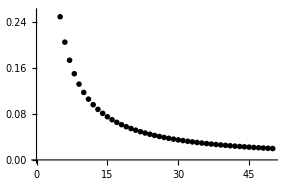

Члены ряда по модулю убывают, условия критерия Лейбница выполнены, следовательно ряд при z=4.5 сходится условно.

Второй при z=3.5

∑_(n=1)^∞ ((-1)^(n+1)2^(n+1)(-1/2)^n)/((n+1)√(ln(n+1)))=∑_(n=1)^∞ -2/((n+1)√(ln(n+1)))=-∑_(n=1)^∞ 2/((n+1)√(ln(n+1)))

не сходится, что было получено выше.

##### Пример №12 .174

Найти область абсолютной сходимости и область равномерной сходимости ряда:

∑_(n=1)^∞ ((n!)^2 z^n)/((2n)!)

Запишем общий член ряда:

```mathematica
f[n_,z_]:=(n!)^2/((2n)!)z^n
```

При помощи признака Даламбера определим область сходимости:

```mathematica
Limit[f[n+1,z]/f[n,z],n->Infinity]
```

z/4

Область сходимости данного ряда |z|<4.

На границе z=4 имеем ряд:

∑_(n=1)^∞ ((n!)^2 4^n)/((2n)!)

По интегральному признаку Коши:

```mathematica
Integrate[f[n,4],{n,1,Infinity}]
```

∫_1^∞ (4^n (n!)^2)/((2 n)!)ⅆn

Он не сходится.

На границе z=-4, ряд

∑_(n=1)^∞ (-1)^n((n!)^2 4^n)/((2n)!)

не удовлетворяет критериям признака Лейбница:

```mathematica
Limit[((n!)^2 4^n)/((2n)!),n-> Infinity]
```

∞

Следовательно он расходится.

Таким образом исходный ряд сходится равномерно на |z|≤ r<4

### 3.2. Разложение функций в ряд Тейлора.

Т е о р е м а  Т е й л о р а. Функция f(z), аналитичная в круге |z-z_0|<R, однозначно представима в этом круге своим рядом Тейлора

f(z)=∑_(n=0)^∞ (c_n(z-z_0))^n,

коэффициенты которого определяются по формулам:

с_n=(f^(n)(z_0))/(n!)=1/(2π ⅈ)∮_(|z-z_0|=r) (f(z))/(z-z_0)^(n+1)ⅆz,n=0,1...

С л е д с т в и е. Если функция f(z) аналитична в области D и z_0∈D, то в круге |z-z_0|<R(z_0,D), где R(z_0,D) - наименьшее расстояние от точки z_0 до границы области D или до ближайшей точки z', в которой f(z) не аналитична, f(z) может быть представлена в виде степенного ряда

f(z)=∑_(n=0)^∞ (f^(n)(z_0))/(n!)(z-z_0)^n

Если z_0=0, то ряд Тейлора также называют рядом Маклорена.

Разложения элементарных функций:

ⅇ^z=1+z+z^2/(2!)+...+z^n/(n!)+...=∑_(n=0)^∞ z^n/(n!),  z∈ℂ

cos z=1-z^2/(2!)+...+(-1)^n z^(2n)/((2n)!)+...=∑_(n=0)^∞ (-1)^n z^(2n)/((2n)!), z∈ℂ

sin z=z-z^3/(3!)+...+(-1)^(n+1)z^(2n+1)/((2n+1)!)+...=∑_(n=0)^∞ (-1)^n z^(2n+1)/((2n+1)!), z∈ℂ

ln(1+z)=z-z^2/2+...+(-1)^(n+1)z^n/n+...=∑_(n=1)^∞ (-1)^(n+1)z^n/n,  |z|<1

arctg z=z-z^3/3+...+(-1)^(n+1)z^(2n+1)/(2n+1)+...=∑_(n=0)^∞ (-1)^(n+1)z^(2n+1)/(2n+1),  |z|<1

(1+z)^a=1+a z+(a(a-1))/(2!)z^2+...+(a(a-1)...(a-n+1))/(n!)z^n=1+∑_(n=1)^∞ Binomial[a,n]z^n,  |z|<1

где Binomial[a,n]=1/(n!)a(a-1)...(a-n+1)

1/(1+z)=1-z+z^2+...+(-1)^n z^n=∑_(n=0)^∞ (-1)^n z^n,  |z|<1

##### Пример №12.214

Разложить функцию в ряд по степеням z :

f(z)=e^(-z^2)

Рассмотрим сначала решение данной задачи “в лоб”. Так как данная нам функция аналитична во всей комплексной плоскости, то для разложения функции в ряд применима формула (8).

Запишем заданную функцию:

```mathematica
f[z_]:=Exp[-z^2]
```

Теперь запишем выражение для n-ого коэффициента с_n:

```mathematica
c[n_]:=D[f[z],{z,n}]/n!/.z->0
```

Так как мы вычисляем разложение в ряд Тейлора в окрестности точки 0, то z_0=0. Такой ряд также называют рядом Маклорена.

Для того чтобы получить окончательный ответ, найдем сумму ряда, например, до 16 члена:

```mathematica
Sum[c[n] z^n,{n,0,16}]
```

1-z^2+z^4/2-z^6/6+z^8/24-z^10/120+z^12/720-z^14/5040+z^16/40320

Запишем данное выражение в виде функции:

```mathematica
r[z_,k_]:=Sum[c[n] z^n,{n,0,k}]
```

Для того чтобы проверить полученный результат, построим графики для исходной функции и ряда до 16 члена:

```mathematica
Plot[{f[z],Evaluate@r[z,16]},{z,-2,2},PlotRange->All]
```

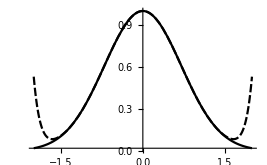

Примечание: функция Evaluate здесь используется для того, чтобы сначала получить разложение в ряд Тейлора, а затем выполнять подстановку в него значений z из отрезка [-2;2].

Увеличивая максимальный порядок разложения, можно добиться сходимости ряда к функции на более широком отрезке.

##### Программный модуль

Составим учебную программу, которая будет выполнять разложение функции в ряд Тейлора по формуле (8).

Имеем следующую тривиальную последовательность действий:

Пусть задана функция f(z)=cos(z).

```mathematica
f[z_]:=Cos[z]
```

1. Записываем функцию коэффициента:

```mathematica
c[n_,z0_]:=D[f[z],{z,n}]/n!/.z->z0
```

2. Находим сумму:

```mathematica
Sum[c[n,0](z-0)^n,{n,0,8}]
```

1-z^2/2+z^4/24-z^6/720+z^8/40320

Соберем это всё в единый модуль:

```mathematica
seriesO[func_,z_,z0_,k_]:=Module[{coef},
coef[n_]:=D[func,{z,n}]/n!/.z->z0;
Sum[coef[n](z-z0)^n,{n,0,k}]]
```

Продемонстрируем пример:

##### Пример №12.215

```mathematica
seriesO[Sin[z]^2,z,0,12]
```

z^2-z^4/3+(2 z^6)/45-z^8/315+(2 z^10)/14175-(2 z^12)/467775

##### Пример №12.242

```mathematica
seriesO[Exp[z^2-4z+1],z,2,12]
```

1/ⅇ^3+(-2+z)^2/ⅇ^3+(-2+z)^4/(2 ⅇ^3)+(-2+z)^6/(6 ⅇ^3)+(-2+z)^8/(24 ⅇ^3)+(-2+z)^10/(120 ⅇ^3)+(-2+z)^12/(720 ⅇ^3)

Напомним, что данный модуль использует формулу (8) для разложения функции в ряд.

Рассмотрим другие пути решения поставленной задачи.

##### Пример №12.231

Используя разложения основных элементарных функций, разложить функцию в ряд по степеням z и указать область сходимости полученного ряда:

f(z)=∫_0^z e^(-t^2/2)ⅆt

На этот раз воспользуемся стандартными разложениями (9)-(15), для того чтобы получить разложение функции в ряд.

Подынтегральная функция - экспоненциальная, значит используя выражение (9), а также замену h=-t^2/2, получим:

```mathematica
seriesO[Exp[h],h,0,8]/.h->-t^2/2
```

1-t^2/2+t^4/8-t^6/48+t^8/384-t^10/3840+t^12/46080-t^14/645120+t^16/10321920

Теперь требуется лишь проинтегрировать полученное выражение:

```mathematica
Integrate[seriesO[Exp[h],h,0,8]/.h->-t^2/2,{t,0,z}]
```

z-z^3/6+z^5/40-z^7/336+z^9/3456-z^11/42240+z^13/599040-z^15/9676800+z^17/175472640

Получили разложение в ряд Тейлора до 17ого члена исходной функции, причем, так как область сходимости ряда (9) - вся комплексная плоскость, то и областью сходимости полученного ряда также является вся комплексная плоскость.

Примечание: если слегка модифицировать модуль, полученный в предыдущем примере:

```mathematica
seriesO1[func_,z_,z0_,k_]:=Module[{coef,t},
coef[n_]:=D[func[t],{t,n}]/n!/.t->z0;
Sum[coef[n](z-z0)^n,{n,0,k}]]
```

то если записать функцию при помощи безымянной переменной, например:

```mathematica
f=Exp[#]&;
```

то, получим следующий результат:

```mathematica
seriesO1[Exp[#]&,-t^2/2,0,8]
```

1-t^2/2+t^4/8-t^6/48+t^8/384-t^10/3840+t^12/46080-t^14/645120+t^16/10321920

```mathematica
Integrate[seriesO1[Exp[#]&,-t^2/2,0,8],{t,0,z}]
```

z-z^3/6+z^5/40-z^7/336+z^9/3456-z^11/42240+z^13/599040-z^15/9676800+z^17/175472640

Также вместо безымянной функции можно использовать просто заголовок подынтегральной функции:

```mathematica
seriesO1[Exp,-t^2/2,0,8]
```

1-t^2/2+t^4/8-t^6/48+t^8/384-t^10/3840+t^12/46080-t^14/645120+t^16/10321920

##### Пример №12.218

Используя разложения основных элементарных функций, разложить функцию в ряд по степеням z и указать область сходимости полученного ряда:

f(z)=(27-z)^(1/3)

Преобразуем выражение:

f(z)=3(1-z/27)^(1/3)

Теперь, пользуясь стандартным разложением (14), при помощи замены t=-z/27 найдем разложение исходной функции в ряд:

При помощи безымянной функции:

```mathematica
seriesO1[3(1+#)^(1/3)&,-z/27,0,6]
```

3-z/27-z^2/2187-(5 z^3)/531441-(10 z^4)/43046721-(22 z^5)/3486784401-(154 z^6)/847288609443

При помощи замены:

```mathematica
seriesO[3(1+t)^(1/3),t,0,6]/.t->-z/27
```

3-z/27-z^2/2187-(5 z^3)/531441-(10 z^4)/43046721-(22 z^5)/3486784401-(154 z^6)/847288609443

Область сходимости ряда определим из:

|t|<1 ⟹|z|<27

##### Встроенные средства

В Wolfram Mathematica функция, которая отвечает за разложение в ряд, имеет следующую структуру: Series[ f[z], {z, z_0, n}] , где n- порядок разложения. Продемонстрируем пример:

```mathematica
Series[ Cos[z],{z,0,5}]
```

1-z^2/2+z^4/24+O[z]^6

Примечание: O[z]^6 , о-малое от z^6 - остаток ряда.

```mathematica
Series[Exp[-z^2],{z,0,16}]
```

1-z^2+z^4/2-z^6/6+z^8/24-z^10/120+z^12/720-z^14/5040+z^16/40320+O[z]^17

```mathematica
Series[Exp[Cos[z]],{z,0,6}]
```

ⅇ-(ⅇ z^2)/2+(ⅇ z^4)/6-(31 ⅇ z^6)/720+O[z]^7

Для того чтобы получить n-ый коэффициент разложения, существует функция SeriesCoefficient[ f[z], {z,z_0,n}]. Примеры:

```mathematica
SeriesCoefficient[Exp[-z^2],{z,0,8}]
```

1/24

```mathematica
SeriesCoefficient[(27-z)^(1/3),{z,0,3}]
```

-5/531441

Также есть возможность получить формулу общего члена:

```mathematica
SeriesCoefficient[Log[1+z],{z,0,n}]
```

Piecewise[{{(-1)^(1+n)/n, n≥1}, {0, True}}]

Если задать n>1, можно избавиться от кусочно-заданной функции:

```mathematica
Refine[SeriesCoefficient[Log[1+z],{z,0,n}],n>1]
```

(-1)^(1+n)/n

Следующая конструкция позволит вывести ответ в формульном виде:

```mathematica
TraditionalForm@Inactivate[Sum[Refine[SeriesCoefficient[Exp[z],{z,0,n}],n>0] z^n, {n,0,Infinity}],Sum]
```

z^n/(n!)n0∞

где функция Inactivate запрещает функции, следующей за ней (Sum), вычислять результат, а TraditionalForm преобразует выражение в традиционный вид.

Составим функцию:

```mathematica
seriesF[f_,z_,z0_]:=TraditionalForm@Inactivate[Sum[Refine[SeriesCoefficient[f,{z,z0,n}],n>5 ](z-z0)^n, {n,0,Infinity}],Sum]
```

Продемонстрируем пример на основе задачи №12.214:

```mathematica
seriesF[Exp[t],t,0]/.t->-z^2
```

((-z^2)^n)/(n!)n0∞

##### Пример №12.232

Разложить функцию в ряд:

f(z)=∫_0^z (sin(t))^2/t ⅆt

Получим разложение подынтегральной функции:

```mathematica
Sin[t]^2/t//TrigReduce
```

(1-Cos[2 t])/(2 t)

Используя стандартное разложение функции cos(h) (10), где h=2t, получаем:

(1-(1-h^2/(2!)+...+(-1)^n h^(2n)/((2n)!)+...))/(2t)=∑_(n=1)^∞ ((-1)^n(2t)^(2n-1))/((2n)!)=∑_(n=1)^∞ ((-1)^n 4^n t^(2n-1))/(2(2n)!)

Теперь применяя теорему о почленном интегрировании получаем:

∫_0^z ∑_(n=1)^∞ ((-1)^(n+1)4^n t^(2n-1))/(2(2n)!)ⅆt=∑_(n=1)^∞ ((-1)^(n+1)4^n)/(2(2n)!)∫_0^z t^(2n-1)ⅆt=∑_(n=1)^∞ ((-1)^(n+1)4^n z^(2n))/(2(2n)!2n)

В итоге получаем ответ:

f(z)=∫_0^z (sin(t))^2/t ⅆt=∑_(n=1)^∞ ((-1)^(n+1)4^(n-1)z^(2n))/((2n)!n),   z∈ℂ.

Проверим полученное аналитическое решение при помощи функции Series:

```mathematica
Series[Integrate[Sin[t]^2/t,{t,0,z}],{z,0,12}]
```

z^2/2-z^4/12+z^6/135-z^8/2520+z^10/70875-z^12/2806650+O[z]^13

```mathematica
Sum[((-1)^(n+1)4^(n-1)z^(2n))/((2n)!n),{n,1,6}]
```

z^2/2-z^4/12+z^6/135-z^8/2520+z^10/70875-z^12/2806650

Ряды совпадают, следовательно мы получили правильный ответ.

##### Пример №12.237

Разложить функцию в ряд по степеням z-z_0 и определить область сходимости полученного ряда:

f(z)=1/(1-z), z_0=3ⅈ

Получим разложение, воспользовавшись опцией Series:

```mathematica
Series[1/(1-z),{z,3I,6}]
```

(1/10+(3 ⅈ)/10)-(2/25-(3 ⅈ)/50) (z-3 ⅈ)-(13/500+(9 ⅈ)/500) (z-3 ⅈ)^2+(7/2500-(6 ⅈ)/625) (z-3 ⅈ)^3+(79/25000-(3 ⅈ)/25000) (z-3 ⅈ)^4+(11/31250+(117 ⅈ)/125000) (z-3 ⅈ)^5-(307/1250000-(249 ⅈ)/1250000) (z-3 ⅈ)^6+O[z-3 ⅈ]^7

Также можно воспользоваться созданным ранее модулем seriesO:

```mathematica
seriesO[1/(1-z),z,3I,6]
```

(1/10+(3 ⅈ)/10)-(2/25-(3 ⅈ)/50) (-3 ⅈ+z)-(13/500+(9 ⅈ)/500) (-3 ⅈ+z)^2+(7/2500-(6 ⅈ)/625) (-3 ⅈ+z)^3+(79/25000-(3 ⅈ)/25000) (-3 ⅈ+z)^4+(11/31250+(117 ⅈ)/125000) (-3 ⅈ+z)^5-(307/1250000-(249 ⅈ)/1250000) (-3 ⅈ+z)^6

Запишем ответ в стандартном виде:

```mathematica
seriesF[1/(1-z),z,3I]
```

(1+3 ⅈ)^(n+1) 10^(-n-1) (z-3 ⅈ)^nn0∞

Область сходимости определим при помощи функции SumConvergence:

```mathematica
SumConvergence[(1+3 I)^(1+n) 10^(-1-n) (-3 I+z)^n,n]
```

√10 Abs[-3 ⅈ+z]<10

В итоге имеем ответ:

1/(1-z)=∑_(n=0)^∞ (1+3ⅈ)^(n+1)/10^(n+1)(z-3ⅈ)^n,  |z-3ⅈ|<√10

##### Пример №12.250

Найти область сходимости указанного ряда и его сумму:

∑_(n=0)^∞ (-1)^n a^(-2n-2)z^(2n), a≠ 0

Для того чтобы найти сумму, преобразуем выражение к:

1/a^2∑_(n=0)^∞ (-1)^n((z/a)^2)^n, a≠ 0

Суммой данной геометрической прогрессии является следующая функция:

1/(1+η)=∑_(n=0)^∞ (-1)^n η^n, где η=(z/a)^2

Область сходимости данной суммы |η|<1

Проверим себя:

```mathematica
Sum[(-1)^n a^(-2n-2)z^(2n),{n,0,Infinity}]
```

1/(a^2+z^2)

Получили тот же самый результат.

Следовательно, получаем ответ:

∑_(n=0)^∞ (-1)^n a^(-2n-2)z^(2n)=1/a^2 1/(1+z^2/a^2)=1/(a^2+z^2), |z|< |a|

## §4. Применение степенных рядов

### 4.1. Интегрирование функций.

Разлагая подынтегральную функцию f(t) в степенной ряд, можно, используя теорему об интегрировании степенных рядов, представить интеграл ∫_0^x f(t)ⅆt в виде степенного ряда и подсчитать величину этого интеграла с заданной точностью при любом значении x из интервала сходимости полученного ряда.

##### Пример №12.289

Разложить указанную функцию в степенной ряд по степеням x:

f(x)=∫_0^x (ln(1+t^2))/t ⅆt

Используем разложение функции ln(1+y):

```mathematica
series[y,0,Log[1+y]]
```

((-1)^(n+1) y^n)/nn0∞

Заменив y→ t^2 и разделив на t, получим ряд:

∑_(n=0)^∞ (-1)^(n+1)t^(2n-1)/n

По теореме о интегрировании степенных рядов получаем:

∫_0^x ∑_(n=0)^∞ (-1)^(n+1)t^(2n-1)/n ⅆt=∑_(n=0)^∞ (-1)^(n+1)/n∫_0^x t^(2n-1)ⅆt=∑_(n=0)^∞ (-1)^(n+1)x^(2n)/(2 n^2)

Ту же последовательность действий можно проделать, используя средства Wolfram Mathematica:

Сразу находим разложение подынтегральной функции:

```mathematica
Series[Log[1+t^2]/t,{t,0,8}]
```

t-t^3/2+t^5/3-t^7/4+O[t]^9

Интегрируем по t от 0 до x и получаем искомый ряд:

```mathematica
Integrate[Series[Log[1+t^2]/t,{t,0,10}],t]/.t-> x
```

x^2/2-x^4/8+x^6/18-x^8/32+x^10/50+O[x]^12

Найти n-ый коэффициент можно следующим образом:

```mathematica
Simplify[SeriesCoefficient[Log[1+t^2]/t,{t,0,n}],n>0]*1/(n+1)
```

(ⅈ ((-ⅈ)^n-ⅈ^n))/(1+n)^2

Множитель 1/(n+1) появился из-за интегрирования функции t^n.

Ответ:

∫_0^x (ln(1+t^2))/t ⅆt=∑_(n=0)^∞ (-1)^(n+1)x^(2n)/(2 n^2)

##### Пример №12.300

Вычислить интеграл с точностью до 10^-5:

∫_0^1 (sin(t))/t ⅆt

Получим разложение заданной функции в ряд :

```mathematica
ser=Integrate[Series[Sin[t]/t,{t,0,10}],t]/.t-> x
```

x-x^3/18+x^5/600-x^7/35280+x^9/3265920-x^11/439084800+O[x]^12

Теперь, заменяя x на нужное нам значение x=1, получаем:

```mathematica
N[Normal@ser/.x-> 1]
```

0.946083

Функция Normal необходима, чтобы отбросить остаток ряда O[x]^12

Получили искомое значение интеграла.

### 4.2. Интегрирование дифференциальных уравнений с помощью рядов.

Степенные ряды широко применяются при решении дифференциальных уравнений. Для целого ряда дифференциальных уравнений показано, что решение y(t) представимо в виде степенного ряда

y(x)=∑_(k=0)^∞ (a_k(x-x_0))^k=∑_(k=0)^∞ (y^(k)(x_0))/(k!)(x-x_0)^k

коэффициенты которого можно определить с учетом заданного уравнения различными способами.

а) Пусть требуется найти решение уравнения y''=f(x,y,y'), удовлетворяющее условиям y(x_0)=y_0, y'(x_0)=y_1, причем функция f(x,y,y') в точке (x_0,y_0,y_1) имеет частные производные любого порядка. Тогда коэффициенты y^(k)(x_0) ряда (1) определяются путем последовательного дифференцирования исходного уравнения и подстановки в него x_0 и найденных уже значений y'(x_0), y''(x_0)...

##### Пример №12.326

Найти решение уравнения, удовлетворяющее заданным условиям:

y''=-x^2y'-2x y+1, y(0)=y'(0)=0

Для того чтобы записать решение в форме (1), продифференцируем данное уравнение несколько раз:

```mathematica
Table[D[y''[x]==-x^2 y'[x]-2x y[x]+1,{x,n}],{n,1,6}]//TableForm
```

y^(3)[x]==-2 y[x]-4 x y'[x]-x^2 y''[x]
y^(4)[x]==-6 y'[x]-6 x y''[x]-x^2 y^(3)[x]
y^(5)[x]==-12 y''[x]-8 x y^(3)[x]-x^2 y^(4)[x]
y^(6)[x]==-20 y^(3)[x]-10 x y^(4)[x]-x^2 y^(5)[x]
y^(7)[x]==-30 y^(4)[x]-12 x y^(5)[x]-x^2 y^(6)[x]
y^(8)[x]==-42 y^(5)[x]-14 x y^(6)[x]-x^2 y^(7)[x]

Теперь можно заметить следующую закономерность, которую мы запишем в виде:

y^(n+2)(x)=-n(n+1)y^(n-1)(x)-2(n+1)x y^(n)(x)-x^2 y^(n+1)(x), при n>2

Подставляя x_0=0 получим, следующее выражение:

y^(n+2)(0)=-n(n-1)y^(n-1)(0)

Или по-другому:

y^(n)(0)=-(n-1)(n-2)y^(n-3)(0)

Мы получили рекуррентное уравнение. Определим начальные условия, два из которых  нам уже даны, а еще одно получается при подстановке x_0=0 в исходное уравнение:

y(0)=y'(0)=0,y''(0)=1

Составим формулу для значения n-ой производной функции y с помощью опции Piecewise:

```mathematica
yn[n_]:=Piecewise[{{-(n-1)(n-2)yn[n-3],n≥3},{1,n==2},{0,n<2}}]
```

Протабулируем функцию от 0 до 12:

```mathematica
Table[yn[n],{n,0,18}]
```

{0,0,1,0,0,-12,0,0,504,0,0,-45360,0,0,7076160,0,0,-1698278400,0}

Мы получили ничто иное как коэффициенты разложения искомой функции в ряд.

Теперь запишем сам ряд по формуле (1):

```mathematica
Sum[yn[k]/(k!)x^k,{k,0,18}]
```

x^2/2-x^5/10+x^8/80-x^11/880+x^14/12320-x^17/209440

Введем функцию y1(x,n):

```mathematica
y1[x_,n_]:=Sum[yn[k]/(k!)x^k,{k,0,n}]
```

y1(x,n) - искомая функция, являющаяся решением исходного дифференциального уравнения.

Решим задачу другим способом.

После того как мы получили рекуррентное уравнение:

y^(n)(0)=-(n-1)(n-2)y^(n-3)(0)

решим его с помощью встроенной функции для решения рекуррентных уравнений RSolve[ expr, f[n], n]:

```mathematica
sol=RSolve[{y[n]==-(n-1)(n-2)y[n-3],y[0]==y[1]==0,y[2]==1},y[n],n]
```

{{y[n]→((-1)^(1/3) 3^(-5/6-n/3) Gamma[5/3] Gamma[1+n] ((-1)^(1+n/3) √3+(-1)^(n/3) √3 Cos[(2 n π)/3]+3 (-1)^(n/3) Sin[(2 n π)/3]))/(2 Gamma[1+n/3])}}

Мы получили громоздкую функцию, однако, если построить список ее значений от 0 до 18, то можно убедиться, что значения коэффициентов совпадают с уже ранее полученными в функции yn(n):

```mathematica
Table[y[n]/.Flatten@sol,{n,0,18}]//N
```

{0.,0.,1.,0.,0.,-12.,0.,0.,504.,0.,0.,-45360.,0.,0.,7.07616×10^6,0.,0.,-1.69828×10^9,0.}

Значения коэффициентов не изменились, значит задавать новую функцию не имеет смысла.

Решим задачу с помощью встроенной в систему функции для решения дифференциальных уравнений DSolve[expr, y[x], x]:

```mathematica
sol1=DSolve[{y''[x]==-x^2 y'[x]-2x y[x]+1,y[0]==y'[0]==0},y[x],x]
```

{{y[x]→-(ⅇ^(-x^3/3) ((-1)^(1/3) x Gamma[2/3]-(-x^3)^(1/3) Gamma[2/3,-x^3/3]))/(3^(1/3) x)}}

Введем функцию y3(x):

```mathematica
y3[x_]:=y[x]/.sol1
```

Докажем графически, что полученная в данном случае функция совпадает с функцией y1(x,18):

```mathematica
Plot[{y3[x],y1[x,18]},{x,0,2}]
```

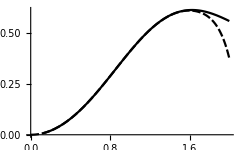

Как мы видим, расхождение начинается примерно с x=1.5, что, разумеется, объясняется малым порядком (n=18) разложения.

Наконец, докажем, что полученное решение верно, непосредственно подставив функцию y3(x) в исходное дифференциальное уравнение:

```mathematica
D[y3[x],{x,2}]==-x^2 D[y3[x],x]-2x y3[x]+1//FullSimplify
```

```mathematica
True
```

Задача решена.

б) Если исходное дифференциальное уравнение линейно относительно искомой функции и ее производных, причем коэффициент при старшей производной в точке x_0 отличен от нуля, то решение следует искать в виде ряда (1) с неопределенными коэффициентами a_k,k=0,1... Законность такого метода вытекает из утверждения, доказываемого в аналитической теории дифференциальных уравнений, которое мы приведем для уравнения 2-ого порядка.

Т е о р е м а 1. Если в дифференциальном уравнении

p_0(x)y''+p_1(x)y'+p_2(x)y=f(x)

функции p(x), p_1(x),p_2(x) и f(x) аналитичны в окрестности точки x_0, и p_0(x_0)≠ 0, то существует решение уравнения (2), представимое в виде степенного ряда (3):

y(x)=∑_(k=0)^∞ (a_k(x-x_0))^k

##### Пример №12.330

Используя степенные ряды, проинтегрировать следующее дифференциальное уравнение:

y''+x y'+y=1, y(0)=y'(0)=0

Введем функцию y(x) по формуле (3):

```mathematica
y[x_]:=Sum[Subscript[a, k] x^k,{k,0,Infinity}]
```

Подставим ее в исходное дифференциальное уравнение:

```mathematica
D[y[x],{x,2}]+x D[y[x],x]+y[x]==1//FullSimplify//TraditionalForm
```

∑_(k=0)^∞ (k-1) k a_k x^(k-2)+x ∑_(k=0)^∞ k a_k x^(k-1)+∑_(k=0)^∞ a_k x^k==1

Учтём начальные условия: при k=0,1 a_k=0, а при k=2 и x=0:

1·2 a_2+0+0=1⇒a_2=1/(2·1)

Теперь составим следующее рекуррентное соотношение:

((k+2)-1)(k+2)a_(k+2)+k a_k+a_k=0
(k+1)(k+2)a_(k+2)=-(k+1)a_k
a_(k+2)=-a_k/(k+2)

Запишем функцию для коэффициента a_k, заданного следующим образом:

a_k=Piecewise[{{-(a_(k-2))/k, k≥ 3}, {1/2, k==2}, {0, k<2}}]

```mathematica
ak[k_]:=Piecewise[{{(-ak[k-2])/k,k≥ 3},{0,k<2},{1/2,k==2}}]
```

Протабулируем функцию на отрезке от 0 до 12:

```mathematica
Table[ak[k],{k,0,12}]
```

{0,0,1/2,0,-1/8,0,1/48,0,-1/384,0,1/3840,0,-1/46080}

Теперь можно записать ряд (3):

```mathematica
Sum[ak[k] x^k,{k,0,12}]
```

x^2/2-x^4/8+x^6/48-x^8/384+x^10/3840-x^12/46080

Данный ряд является решением исходного дифференциального уравнения при заданных начальных условиях. Зададим функцию y1(x,n):

```mathematica
y1[x_,n_]:=Sum[ak[k] x^k,{k,0,n}]
```

Теперь решим ту же задачу, используя функцию DSolve:

```mathematica
sol=DSolve[{D[y[x],{x,2}]+x D[y[x],x]+y[x]==1,y[0]==0,y'[0]==0},y[x],x]
```

{{y[x]→ⅇ^(-x^2/2) (-1+ⅇ^(x^2/2))}}

```mathematica
y2[x_]:=ⅇ^(-x^2/2) (-1+ⅇ^(x^2/2))
```

Построим график функций y1(x,24) и функции полученной с помощью DSolve:

```mathematica
Plot[{y2[x],y1[x,24]},{x,-4,4}]
```

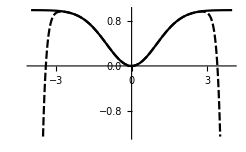

Так как функции совпадают приблизительно до |x|=2.5, будем считать, что решение в окрестности точки x_0=0 получено верно.

Еще в этом можно убедится, подставив функцию в общем виде в исходное дифференциальное уравнение:

```mathematica
D[y2[x],{x,2}]+x D[y2[x],x]+y2[x]==1//FullSimplify
```

True

Получили верное равенство.

Замечание: в том что ряд был получен верно, можно также убедиться, разложив функцию y2(x)  в ряд по степеням x:

```mathematica
Series[y2[x],{x,0,12}]
```

x^2/2-x^4/8+x^6/48-x^8/384+x^10/3840-x^12/46080+O[x]^13

Ряды совпадают, значит на данном этапе будем считать, что решение получено верно.

### 4.3. Уравнение и функции Бесселя.

Частным случаем уравнения (2) является уравнение Бесселя

x^2 y''+x y'+(x^2-v^2)y=0

Его решениями являются цилиндрические функции Бесселя первого рода порядка v

J_v(x)=a_0^(v)x^v∑_(k=0)^∞ (-1)^k/(k!(v+1)(v+2)...(v+k))(x/2)^(2k)

и для нецелых v

J_-v(x)=a_0^(v)x^-v∑_(k=0)^∞ (-1)^k/(k!(1-v)(2-v)...(k-v))(x/2)^(2k)

Если же v - целое число, v=n, то вторым частным решением уравнения Бесселя (4) является функция Неймана (или Вебера), определяемая из соотношения

N_n(x)=lim_(v→n) (I_v(x)cos v π-I_-v(x))/(sin v π)

являющаяся цилиндрической функцией второго рода порядка n.

Формулы (5) и (6) можно упростить с помощью гамма-функции, которая определена равенством

Г(v)=∫_0^(+∞) ⅇ^-x x^(v-1)ⅆx

Этот несобственный интеграл сходится для всех v>0. Гамма-функция - обобщение для x>0 функции факториала n!, которая определена только если n - натуральное число. Рассмотрим предел:

(Г(1)=∫_0^(+∞) ⅇ^-x ⅆx=lim_(b→+∞) -ⅇ^-x|)_0^b=1

Теперь найдем интеграл:

(Г(v+1)=∫_0^(+∞) ⅇ^-x x^v ⅆx=Г(1)=lim_(b→+∞) -ⅇ^-x x^v|)_0^b+∫_0^(+∞) v ⅇ^-x x^(v-1)ⅆx=
=v ∫_0^(+∞) ⅇ^-x x^(v-1)ⅆx

Таким образом мы получаем равенство:

Г(v+1)=v Г(v)

Это важнейшее свойство гамма-функции.

Г(2)=1· Г(1)=1!, Г(3)=2·Г(2)=2!,..., Г(n+1)=n!

Теперь, если положить a_0^(v)  в формулах (5) и (6)

a_0^(v)=1/(2^v Г(v+1))

и заметить, что

Г(v+k+1)=(v+k)(v+k-1)...(v+2)(v+1)Г(v+1)

то тогда можно записать функцию Бесселя первого рода кратко с помощью гамма-функции:

J_v(x)=∑_(k==0)^∞ (-1)^k/(k!Г(v+k+1))(x/2)^(2k+v)

J_-v(x)=∑_(k=0)^∞ (-1)^k/(k!Г(-v+k+1))(x/2)^(2k-v)

Параметрическое уравнение Бесселя порядка v имеет вид:

x^2 y''+x y'+(α^2 x^2-v^2)y=0, α>0

Заменой t=α x преобразовываем это уравнение в стандартное уравнение Бесселя:

t^2 y''+t y'+(t^2-v^2)y=0

Имеющее общее решение:

y(x)=c_1 J_v(α x)+c_2 J_-v(α x)- если v - не целое число,
y(x)=c_1 J_v(α x)+c_2 N_v(α x)- если v -  целое число.

##### Пример №12.342

Найти общее решение уравнения

x^2 y'' +x y'+ (9 x^2-1/25)y=0

Функция Бесселя в Mathematica записывается BesselJ[v,x]. Построим два графика: J_(1/5)(3x) и J_(-1/5)(3x):

```mathematica
Plot[{BesselJ[1/5,x],BesselJ[-1/5,x]},{x,0,15},PlotLabels->{"J_(1/5)(3x)","J_(-1/5)(3x)"}]
```

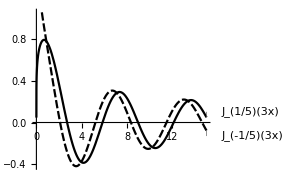

Ответом, общим решением этого параметрического уравнения, является функция y(x), определяемая:

y(x)=c_1 J_(1/5)(3x)+c_2 J_(-1/5)(3x)

## §5. Ряды Лорана

### 5.1. Ряды Лорана. Теорема Лорана.

Рядом Лорана называется ряд

f(z)=∑_(n=-∞)^∞ (c_n(z-z_0))^n

при этом ряд

f_2(z)=∑_(n=-∞)^-1 (c_n(z-z_0))^n

называется главной частью ряда Лорана, а ряд

f_3(z)=∑_(n=0)^∞ (c_n(z-z_0))^n

- правильной частью. Если

lim_(n→∞) (|c_-n|)^(1/n)=r<R=1/(lim_(n→∞) (|c_n|)^(1/n))

то областью сходимости ряда (1) является кольцо K={ z| 0≤ r< |z-z_0|<R}. В этом кольце К сумма ряда f(z)=f_1(z)+f_2(z) является функцией аналитической, причем коэффициенты ряда c_n связаны с функцией f(z) посредством формул

c_n=1/(2π ⅈ)∫_(|z-z_0|=r') (f(z))/(z-z_0)^(n+1)ⅆz,     где r<r'<R, n+1>0

Причем если функция f(z) аналитичная в кольце |z-z_0|=r', то коэффициенты разложения будут вычисляться по формуле:

c_n=1/(n!)(ⅆ^n/(ⅆ z^n)f)(z_0)

Т е о р е м а  Л о р а н а. Если функция f(z) аналитична в кольце 0≤ r< |z-z_0|<R, то в этом кольце она единственным образом представима в виде ряда Лорана (1), коэффициенты которого вычисляются по формулам (2).

В данном разделе решение будем приводить методами функционального и алгоритмического программирования, в отличии от традиционных рутинных “бумажных” решений.

Использование подобных методов позволяет оптимальнее решать задачи, в чем и заключается преимущество Mathematica.

##### Пример №12.352

Найти все разложения указанной функции в ряд Лорана по степеням z-z_0 и установить области сходимости полученных разложений:

f(z)=1/(z(z-1)),  z_0=1

Сначала рассмотрим детальное решение данной задачи. Затем усложним ее, так как на исходном примере нельзя отследить все этапы, необходимые для понимания общего алгоритма. И потом, наконец, составим программу разложения функций в ряд Лорана.

Запишем функцию:

```mathematica
f[z_]:=1/(z(z-1))
```

Из структуры функции видно, что её аналитичность  нарушается в точках z_0=1, z_1=0. Следовательно функция будет аналитична в кольцах: 1) 0< |z-1|< 1  2) |z-1| >1

Изобразим точки z_1 и z_2, а также контуры интегрирования r1 и r2, которые находятся соответственно в кольце 1) и 2):

```mathematica
Graphics[{Circle[{0,0},0.3],Circle[{1,0},0.6],Circle[{1,0},2],PointSize[Large],Point[{0,0}],Point[{1,0}],Text[r1,{0.6,0.6}],Text[r2,{2,2}] ,Text[γ,{0.3,0.3}]   },PlotRange->{{-3,3},{-3,3}},Axes->True]
```

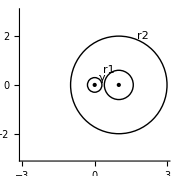

Для того чтобы найти разложение в ряд Лорана в окрестности точки z_0, достаточно воспользоваться уже известной нам функцией Series,о которой говорится в разделе Ряды Тейлора и которая имеет вид: Series[ f[z], {z,z_0,n}] :

```mathematica
Series[f[z],{z,1,5}]
```

1/(z-1)-1+(z-1)-(z-1)^2+(z-1)^3-(z-1)^4+(z-1)^5+O[z-1]^6

Получим выражение для n-ого коэффициента:

```mathematica
SeriesCoefficient[f[z],{z,1,n}]
```

Piecewise[{{1, n==-1}, {(-1)^(1+n), n≥0}, {0, True}}]

Запишем n-ый коэффициент как функцию от n. Это понадобится нам в дальнейшем:

```mathematica
c1[n_]:=Piecewise[{{(-1)^(n+1),n≥ -1},{0,n<-1}}]
```

Таким образом, мы получили разложение:

f(z)=∑_(n=-1)^∞ (-1)^(n+1)(z-1)^n   , при 0< |z-1| <1

Для того чтобы найти разложение в кольце|z-1| >1, воспользуемся формулой (2):

c_n=∮_(|z-1|=R) (f(z))/(z-1)^(n+1)ⅆz, где R>1

Согласно теореме Коши для многосвязной области имеем:

∮_(|z-1|=R) (f(z))/(z-1)^(n+1)ⅆz=∮_(|z-1|=r') (f(z))/(z-1)^(n+1)ⅆz+∮_(|z|=r') (f(z) ·z)/((z-1)^(n+1)·z)ⅆz, где 0<r'<1

Здесь первый интеграл есть разложение в ряд Лорана в кольце 0< |z-1|<1 и уже вычислен, а второй интеграл, исходя из интегральной формулы Коши, будет равен:

∮_(|z|=r') (f(z) ·z^u)/((z-1)^(n+1)·z^u)ⅆz=1/(u!)(ⅆ^(u-1)/(ⅆ z^(u-1))(f(z) ·z^u)/(z-1)^(n+1))(0), где u- кратность корня z=0  в уравнении Denominator[f(z)]=0

Теперь запишем функцию c2 от n:

```mathematica
c2[n_]:=Simplify[f[z] z/(z-1)^(n+1)]/.z->0
```

Протабулируем функцию c2(n)  на отрезке от -8 до 8

```mathematica
Table[{n,c2[n]},{n,-8,8}]
```

{{-8,1},{-7,-1},{-6,1},{-5,-1},{-4,1},{-3,-1},{-2,1},{-1,-1},{0,1},{1,-1},{2,1},{3,-1},{4,1},{5,-1},{6,1},{7,-1},{8,1}}

В нашем обозначении из (4) следует:

c_n=c_(1n)+c_(2n)

Отобразим множество вида { n, c_n }, -8≤ n≤ 8:

```mathematica
Table[{n,c1[n]+c2[n]},{n,-8,8}]
```

{{-8,1},{-7,-1},{-6,1},{-5,-1},{-4,1},{-3,-1},{-2,1},{-1,0},{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0}}

Как мы видим, коэффициенты при степени большей -2, равны 0.

Конечно, в нашем конкретном случае функция общего члена c(n) легко определяется, однако воспользуемся функцией FindSequenceFunction, которая, как следует из названия, находит функцию из последовательности. Она имеет следующую структуру: FindSequenceFunction[ { {n_-k,a_k}....{n_0,a_0}....{n_q,a_q}}, n]. Применим ее к последовательности, начинающейся при n=-2 и до n=-8.

```mathematica
FindSequenceFunction[Table[{n,c2[n]},{n,-8,-2}],n]
```

(-1)^(10+n)

Итак, запишем разложение в ряд Лорана в кольце |z-1| >1:

```mathematica
Sum[(z-1)^n(c1[n]+c2[n]),{n,-8,8}]
```

1/(-1+z)^8-1/(-1+z)^7+1/(-1+z)^6-1/(-1+z)^5+1/(-1+z)^4-1/(-1+z)^3+1/(-1+z)^2

В общем виде:

f(z)=∑_(n=2)^∞ (-1)^n/(z-1)^n, при  |z-1| >1

Рассмотрим более сложный пример.

##### Пример №2

Найти все разложения указанной функции в ряд Лорана по степеням z-z_0 и установить области сходимости полученных разложений:

f(z)=1/((z-2)^2(z+3)^3), z_0=-3

В данной задаче представлена более сложная функция с несколькими точками потери аналитичности разной кратности.

Запишем функцию:

```mathematica
f[z_]:=1/((z-2)^2(z+3)^3)
```

Для того чтобы найти кольца аналитичности, решим уравнение f[z]^-1=0 или просто приравняем знаменатель к 0. Для того чтобы получить знаменатель функции f(z), будем использовать опцию Denominator[ f[z] ]

```mathematica
sol=z/.Solve[Denominator[f[z]]==0,z]
```

{-3,-3,-3,2,2}

Следующим пунктом в нашем алгоритме будет определение кратности каждого корня. Воспользуемся тем же методом, что и в главе 1 параграфе 4 “Интегралы”. Там мы определяли кратность при помощи функции Counts[list]:

```mathematica
rul=Counts[sol]
```

<|-3→3,2→2|>

Теперь запишем функцию кратности i-ого корня:

```mathematica
sol=DeleteDuplicates[sol];
u[i_]:=sol[[i]]/.rul
```

Теперь нужно разделить комплексную плоскость на окружности. Изобразим графически:

```mathematica
Graphics[{Circle[{-3,0},3],Circle[{2,0},0.6],Circle[{-3,0},6],PointSize[Large],Point[{-3,0}],Point[{2,0}],Text[r1,{0.6,0.6}],Text[r2,{2,2}] ,Text[γ,{2.7,0.6}]   },PlotRange->{{-8,8},{-8,8}},Axes->True]
```

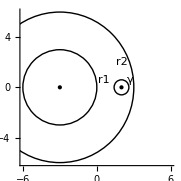

Для того чтобы аналитически определить кольца сходимости, поступим следующим образом: возьмем точку z_0-центр разложения и будем сравнивать расcтояние от нее до корней z_1....z_n. Наименьшее раcстояние будет соответствовать верхней границе первого кольца и нижней границе второго кольца, верхней же границе второго кольца будет соответствовать уже наименьшее раcстояние до следующего корня, и так далее. Составим множество границ колец, используя функцию Sort[ list ], которая располагает элементы list  в порядке возрастания. Сортировать же мы будем множество всех раcстояний от z_0 до z_i:

```mathematica
a=With[{z0=-3},Sort[Table[Abs[-z0+sol[[i]]],{i,1,Length[sol]}]]]
```

{0,5}

Первый элемент равен нулю - следовательно центр разложения z_0 совпадает с одним из корней.

Получили 2 кольца: 1) 0< |z+3|<5 и 2)|z+3| >5

Разложение в окрестности z_0 всегда можно отыскать с помощью функции Series:

```mathematica
Series[f[z],{z,-3,5}]
```

1/(25 (z+3)^3)+2/(125 (z+3)^2)+3/(625 (z+3))+4/3125+(z+3)/3125+(6 (z+3)^2)/78125+(7 (z+3)^3)/390625+(8 (z+3)^4)/1953125+(9 (z+3)^5)/9765625+O[z+3]^6

Получим формулу n-ого коэффициента:

```mathematica
c0=SeriesCoefficient[f[z],{z,-3,n}]
```

Piecewise[{{3/625, n==-1}, {2/125, n==-2}, {1/25, n==-3}, {5^(-5-n) (4+n), n≥0}, {0, True}}]

Составим функцию c_1(n)  - коэффициента разложения в кольце 1):

```mathematica
c1[k_]:=c0/.n->k
```

Итак, получили:

f(z)=∑_(n=-3)^∞ ((4+n)(z+3)^n)/5^(5+n), при 0< |z+3|<5

Разложение в кольце 2) |z+3| >5 будем искать аналогично формуле (4):

c_(2n)=1/(1!)ⅆ/ⅆz(f(z)(z-2)^2)/(z+3)^(n+1),z→ 2

Запишем выражение для коэффициента c_2(n):

```mathematica
c2[n_]:=D[Simplify[f[z](z-sol[[2]])^u[2]/(z+3)^(n+1)],{z,u[2]-1}]/.z->2
```

```mathematica
Table[{n,c2[n]},{n,-8,8}]
```

{{-8,500},{-7,75},{-6,10},{-5,1},{-4,0},{-3,-1/25},{-2,-2/125},{-1,-3/625},{0,-4/3125},{1,-1/3125},{2,-6/78125},{3,-7/390625},{4,-8/1953125},{5,-9/9765625},{6,-2/9765625},{7,-11/244140625},{8,-12/1220703125}}

Итак, теперь, для того чтобы найти разложение в кольце, внутренний контур которого охватывает все особые точки, нужно вычислить сумму коэффициентов c(n)=c_1(n)+c_2(n):

```mathematica
Sum[(z+3)^n(c1[n]+c2[n]),{n,-12,8}]
```

625000/(3+z)^12+109375/(3+z)^11+18750/(3+z)^10+3125/(3+z)^9+500/(3+z)^8+75/(3+z)^7+10/(3+z)^6+1/(3+z)^5

Найдем формулу коэффициента n:

```mathematica
c22[k_]:=FindSequenceFunction[Table[{n,c1[n]+c2[n]},{n,-12,-5}],j]/.j->k
```

```mathematica
c22[n]
```

-5^(-5-n) (4+n)

Из получившейся последовательности действий видно, что каждый раз при увеличении радиуса кольца разложения (выход за предел текущего кольца) общий коэффициент разложения будет увеличиваться на c_i(n).

В итоге, получили:

f(z)=(-∑)_(n=-∞)^-5((4+n)(z+3)^n)/5^(5+n), при |z+3| >5

f(z)=∑_(n=-3)^∞ ((4+n)(z+3)^n)/5^(5+n), при 0< |z+3|<5

##### Общий алгоритм

Проанализировав последовательность действий, создадим программный модуль разложения в ряд Лорана:

```mathematica
loranO[z_,expr_  ,z0_,r_,k_]:=Module[{sol,sol1,u,c0,c1},
c0[n_]:=Evaluate[SeriesCoefficient[expr,{z,z0,n}]];
sol1=z/.Solve[0<Abs[z-z0]<r&&Denominator[Simplify[TrigToExp[expr]]]==0,z];
c1[n_]:=0;
If[sol1≠ {},
sol=DeleteDuplicates[sol1];
u[i_]:=sol[[i]]/.Counts[sol1];
c1[n_]:=Sum[1/((u[i]-1)!)Limit[D[Simplify[expr(z-sol[[i]])^u[i]/(z-z0)^(n+1)],{z,u[i]-1}],z-> sol[[i]]],{i,1,Length[sol]}]];
Sum[(z-z0)^n(c0[n]+c1[n]),{n,-k,k}]]
```

Итак, данный модуль имеет следующую построчную структуру:

1. Запись коэффициента c0[n] разложения в ряд в окрестности z_0.

2. Поиск тех корней знаменателя, которые расположены не дальше r - кольца разложения, не включая корень z0.

3. В случае если множество корней не пустое множество, определение кратности каждого корня.

4. Вычисление коэффициентов c_i[n] по формуле (4).

5. Запись получившегося разложения.

Продемонстрируем пример работы:

##### Пример №12.354

```mathematica
loranO[z,1/((z-2)(z+3)),2,6,8]
```

15625/(-2+z)^8-3125/(-2+z)^7+625/(-2+z)^6-125/(-2+z)^5+25/(-2+z)^4-5/(-2+z)^3+1/(-2+z)^2

##### Пример №12.364

```mathematica
loranO[z,z/((z^2+1)^2),I,3,8]
```

-(112 ⅈ)/(-ⅈ+z)^8+48/(-ⅈ+z)^7+(20 ⅈ)/(-ⅈ+z)^6-8/(-ⅈ+z)^5-(3 ⅈ)/(-ⅈ+z)^4+1/(-ⅈ+z)^3

##### Пример № х

```mathematica
loranO[z,1/Sin[z],0,Pi+1,8]
```

-(2 π^6)/z^7-(2 π^4)/z^5-(2 π^2)/z^3-1/z+(1/6-2/π^2) z+(7/360-2/π^4) z^3+(31/15120-2/π^6) z^5+(127/604800-2/π^8) z^7

Созданную функцию будем использовать при необходимости в дальнейшем.

### 5.2. Характер изолированных особых точек

Точка z_0 называется правильной точкой для аналитической в области D функции f(z), если существует степенной ряд ∑_(n=0)^∞ c_n(z_0) (z-z_0)^n с радиусом сходимости r(z_0)>0 такой, что в общей части круга сходимости |z-z_0|<r(z_0) и области D сумма этого ряда ϕ_z_0(z) совпадает с f(z). Точки, не являющиеся правильными, называются особыми.

Точка z_0 называется изолированной особой точкой функции f(z) , если f(z)  - однозначная аналитическая функция в кольце 0< |z-z_0|<R, а z_0 - особая точка.

Аналогично, точка z_0=∞ называется изолированной особой точкой функции f(z), если f(z)  - однозначная аналитическая функция в кольце r< |z| <∞ и z=∞ - особая точка.

Изолированная особая точка z_0 функции f(z) называется:

Устранимой особой точкой, если существует конечный предел:

lim_(z→z_0) f(z)=a≠ ∞

Полюсом порядка m≥ 1, если для функции g(z)=(f(z))^-1 точка z_0 является нулем порядка m. Если z_0 - полюс, то

lim_(z→z_0) f(z)= ∞

Существенно особой если конечного предела не существует:

lim_(z→z_0) f(z)- не существует

##### Пример №12.382

Указать все конечные особые точки заданной ниже функции и определить их характер:

f(z)=1/((z^2+i)^3)

Запишем функцию:

```mathematica
f[z_]:=1/((z^2+I)^3)
```

Для того чтобы найти особые точки, решим уравнение Denominator[f[z]]=0:

```mathematica
sol=Flatten[Solve[Denominator[f[z]]==0,z]]
```

{z→-(-1)^(3/4),z→-(-1)^(3/4),z→-(-1)^(3/4),z→(-1)^(3/4),z→(-1)^(3/4),z→(-1)^(3/4)}

Мы получили 2 корня кратности 3. Для того чтобы избавиться от повторов, воспользуемся функцией DeleteDuplicates.

```mathematica
sol=DeleteDuplicates[sol]
```

{z→-(-1)^(3/4),z→(-1)^(3/4)}

Теперь исследуем характер полученных особых точек. Найдем предел в точке z=-(-1)^(3/4):

```mathematica
Limit[f[z],sol[[1]]]
```

(-1)^(3/4) ∞

Получили, что точка z=-(-1)^(3/4) является полюсом третьего порядка.

Проделаем то же самое для второй точки z=(-1)^(3/4):

```mathematica
Limit[f[z],sol[[2]]]
```

(1-ⅈ)/(√2) ∞

Получается, что обе точки являются полюсами третьего порядка.

##### Пример 12.388

Указать все конечные особые точки заданной ниже функции и определить их характер:

f(z)=(z(π-z))/(sin(2z))

Запишем функцию:

```mathematica
f[z_]:=(z(Pi-z))/Sin[2z]
```

Решим уравнение вида f^-1(z):

```mathematica
sol=Solve[f[z]^-1==0,z]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{}

Так как в математике наша функция выглядит как f(z)=(π-z) z Csc[2 z],  появляются трудности с решением уравнения вида Csc[2z]^-1=0. Для того чтобы решить эту проблему можно задав круг, в котором будем искать корни уравнения (f(z))^-1=0:

```mathematica
sol=Solve[Abs[z]<10&&f[z]^-1==0,z]
```

{{z→-3 π},{z→-(5 π)/2},{z→-2 π},{z→-(3 π)/2},{z→-π},{z→-π/2},{z→π/2},{z→(3 π)/2},{z→2 π},{z→(5 π)/2},{z→3 π}}

Отсюда общее множество решений можно записать в виде:

```mathematica
soln[n_]:=z->Pi/2 n
```

Из структуры функции видно, что особенно интересны для нас точки z=0 и z=π. Исследуем функцию в данных точках:

```mathematica
Limit[f[z],soln[0]]
```

π/2

```mathematica
Limit[f[z],soln[2]]
```

-π/2

Обе точки являются устранимыми особыми точками, так как в них существует конечный предел (1).

Все остальные корни уравнения (4) будут являться полюсами первого порядка. Докажем это:

```mathematica
Table[{soln[i],Limit[f[z],soln[i]]},{i,-4,4}]
```

{{z→-2 π,1/((ⅈ+4 π^2)^3)},{z→-(3 π)/2,64/((4 ⅈ+9 π^2)^3)},{z→-π,1/((ⅈ+π^2)^3)},{z→-π/2,64/((4 ⅈ+π^2)^3)},{z→0,ⅈ},{z→π/2,64/((4 ⅈ+π^2)^3)},{z→π,1/((ⅈ+π^2)^3)},{z→(3 π)/2,64/((4 ⅈ+9 π^2)^3)},{z→2 π,1/((ⅈ+4 π^2)^3)}}

Итак, имеем, что:

z_0=0,z_0=π - устранимые особые точки
z_0=(π k)/2, k=±1,-2,±3... - полюса первого порядка.

##### Пример 12.391

Указать все конечные особые точки заданной ниже функции и определить их характер:

f(z)=ⅇ^(1/(z-3ⅈ))

```mathematica
f[z_]:=Exp[1/(z-3I)]
```

Изучим точку z=3ⅈ:

```mathematica
f[z]//ComplexExpand
```

ⅇ^(z/(9+z^2)) Cos[3/(9+z^2)]+ⅈ ⅇ^(z/(9+z^2)) Sin[3/(9+z^2)]

Эта точка будет существенно особой для функции f(z), так как:

lim_(z→3 ⅈ) sin(3/(z^2+9)) не имеет конечного значения

Ответ:

z_0=3ⅈ - существенно особая точка

##### Пример 12.399

Для заданной функции выяснить характер бесконечно удаленной особой точки:

f(z)=(3 z^5-5z+2)/(z^2+z-4)

```mathematica
f[z_]:=(3 z^5-5z+2)/(z^2+z-4)
```

Для того чтобы исследовать бесконечно удаленную особую точку, проведем замену: z=1/η

```mathematica
f[1/η]//Simplify
```

(3-5 η^4+2 η^5)/(η^3+η^4-4 η^5)

Исследуем точку η=0:

```mathematica
Limit[f[1/η],η->0]
```

∞

Следовательно точка z_0=∞, бесконечно удаленная, является полюсом функции f(z)

## §6. Вычеты и их применение.

### 6.1. Вычет функции и его вычисление.

Если функция f(z) аналитична в некоторой окрестности точки z_0, за исключением может быть самой точки z_0, то вычетом функции f(z) относительно точки z_0, обозначаемым res[f(z), z→ z_0]или res[f(z),z_0] называется число, равное значению интеграла 1/(2π ⅈ)∫_C f(z)ⅆz, где С - некоторый замкнутый контур, лежащий в области аналитичности f(z) и содержащий внутри себя только одну особую точку z_0.

Вычет функции совпадает с коэффициентом с_-1 разложения f(z) в ряд Лорана по степеням z - z_0, т.е.

res[f(z),z_0]=c_-1=1/(2 π ⅈ)∫_(|z-z_0|=r) f(z)ⅆz

Если z_0=∞ - изолированная особая точка функции f(z), то

res[f(z),∞]=1/(2 π ⅈ)∫_(С_R^-) f(z)ⅆz

где С_R^-={z| |z|=R}, R достаточно велико и обход контура - по часовой стрелке. Заметим, что если

f(z)=∑_(n=-∞)^∞ c_n z^n,          r< |z| <∞,
c_n=1/(2 π ⅈ)∫_(|z|=R>r) (f(z))/z^(n+1)ⅆz, n= 0,±1,±2,  то

res[f(z),∞]=-с_-1.

Если z_0 - полюс первого порядка функции f(z), то

res[f(z),z_0]=lim_(z→z_0) (z-z_0)f(z)

Если z_0- полюс порядка m≥2 функции f(z), то

res[f(z),z_0]=1/((m-1)!)  lim _(z→z_0) ⅆ^(m-1)/(ⅆ z^(m-1)) ((z-z_0)^m f(z))

##### Пример №12.416

Найти вычеты указанной функции относительно каждого из его полюсов, отличных от ∞

f(z)=ⅇ^z/(z^2(z^2+9))

Найдем каждый полюс заданной функции:

```mathematica
f[z_]:=E^z/(z^2(z^2+9))
```

Для того чтобы найти особые точки функции f(z), решим уравнение вида: (f(z))^-1=0.

```mathematica
sol=z/.Solve[f[z]^-1==0,z]
```

{0,0,-3 ⅈ,3 ⅈ}

Для того чтобы найти вычет в точке, воспользуемся функцией Residue[f[z],{z,z_0}], которая находит вычет функции f(z) в точке z_0.

```mathematica
Residue[f[z],{z,0}]
```

1/9

Это можно проделать для каждого полюса, но если представить, что имеется очень много полюсов, то искать вычет в каждом отдельно - довольно трудоемкая задача.

Найдем вычеты сразу во всех точках множества полюсов.

```mathematica
Table[ {sol[[i]],Residue[f[z],{z,sol[[i]]}]},{i,1,Length[sol]}] // DeleteDuplicates
```

{{0,1/9},{-3 ⅈ,-1/54 ⅈ ⅇ^(-3 ⅈ)},{3 ⅈ,1/54 ⅈ ⅇ^(3 ⅈ)}}

Элементы данного множества имеют вид: z_0 , res(f(z), z_0).

Получили три полюса, причем один из них второго порядка (z_0=0), и вычеты в каждом из них.

##### Пример №12.413

Найти вычеты указанной функции относительно каждого из его полюсов, отличных от ∞

f(z)=1/(sin(z)-1/2)

Запишем функцию f(z) и найдем полюса, решив уравнение (f(z))^-1=0:

```mathematica
f[z_]:=1/(Sin[z]-1/2)
```

```mathematica
sol=Solve[f[z]^-1==0,z]
```

{{z→ConditionalExpression[π/6+2 π C[1],C[1]∈Integers]},{z→ConditionalExpression[(5 π)/6+2 π C[1],C[1]∈Integers]}}

Получили бесконечное число решений, следовательно и полюсов. Перепишем решение в более привычный для нас вид:

```mathematica
sol1={{z-> π/6+2π n},{z-> (5π)/6+2π n}};
```

Или, если записать одним выражением:

```mathematica
sol2=(-1)^n π/6+π n;
```

Если функция периодична, то и функция вычета от  n также будет периодичной. Докажем это составив множество {z_0(n), Res(f(z), z→z_0(n))}

```mathematica
Table[{sol2,Residue[f[z],{z,sol2}]},{n,-3,3}]
```

{{-(19 π)/6,-2/(√3)},{-(11 π)/6,2/(√3)},{-(7 π)/6,-2/(√3)},{π/6,2/(√3)},{(5 π)/6,-2/(√3)},{(13 π)/6,2/(√3)},{(17 π)/6,-2/(√3)}}

Ответ:

res[f(z),(-1)^n π/6+π n]=(-1)^n 2/(√3)

В таком же порядке следует решать задачи №№12.408-12.423.

##### Общий алгоритм

Составим программный модуль, который для любой функции f(z) в кольце |z-a|<b будет находить все полюса, а затем вычислять в них вычет.

Действовать он будет следующим образом:

1. Решение уравнения f^-1(z)=0  при условии |z_k-a|<b.

2. Составление множества типа {z_k,res[f(z),z_k]}

```mathematica
residueK[z_,func_,a_,b_]:=Module[{sol},
sol=z/.Solve[Abs[z-a]<b&&func^-1==0,z]//DeleteDuplicates;
Table[{sol[[i]],Residue[func,{z,sol[[i]]}]},{i,1,Length[sol]}]
]
```

Продемонстрируем пример его работы:

```mathematica
residueK[z,E^z/(z^2(z^2+9)),0,10]
```

{{0,1/9},{-3 ⅈ,-1/54 ⅈ ⅇ^(-3 ⅈ)},{3 ⅈ,1/54 ⅈ ⅇ^(3 ⅈ)}}

```mathematica
residueK[z,1/(Sin[z]-1/2),0,10]
```

{{-(19 π)/6,-2/(√3)},{-(11 π)/6,2/(√3)},{-(7 π)/6,-2/(√3)},{π/6,2/(√3)},{(5 π)/6,-2/(√3)},{(13 π)/6,2/(√3)},{(17 π)/6,-2/(√3)}}

Примечание: Данный модуль работает лишь с теми функциями, в которых полюс является нулём функции g(z)=f^-1(z). С более сложными функциями он справиться не может.

Рассмотрим следующий номер:

##### Пример №12.424

Найти вычеты функции относительно точки z_0=0:

f(z)=e^(1/z), z_0=0

Введем заданную функцию:

```mathematica
f[z_]:=Exp[1/z]
```

Точка z_0=0 для нее является существенно особой, так как не существует предела функции при z→ z_0 :

```mathematica
Limit[Cos[1/z]+I Sin[1/z],z->0]
```

ⅈ Interval[{-1,1}]+Interval[{-1,1}]

Попытаемся воспользоваться встроенной функцией Residue:

```mathematica
Residue[f[z],{z,0}]
```

Residue[ⅇ^(1/z),{z,0}]

Никакого результата мы не получили.

Для нахождения вычета определим коэффициент c_-1 разложения функции e^(1/z) в ряд Лорана по степеням z .

Функция разложения в ряд Series также не дала нам нужного результата.

```mathematica
Series[f[z],{z,0,4}]
```

ⅇ^(1/z)

Известно разложение в ряд функции ⅇ^η:

ⅇ^η=∑_(n=0)^∞ η^n/(n!)

а также то, что данный ряд сходится на всей комплексной плоскости. Поэтому заменим η=1/z. Тогда получается ряд:

ⅇ^(1/z)=∑_(n=0)^∞ 1/(n!)(1/z)^n

Запишем это разложение следующим образом:

```mathematica
Normal[Series[Exp[p],{p,0,4}]]/.p-> 1/z
```

1+1/(24 z^4)+1/(6 z^3)+1/(2 z^2)+1/z

Отсюда видно, что  коэффициент c_-1=1. Следовательно ответ:

res(e^(1/z),z→0)=1

Примечание: номера №12.425,426 имеют точно такой же ход решения, поэтому рекомендуются к самостоятельному решению.

##### Пример №12.427

Найти вычеты функции относительно точки z_0=∞

f(z)=sin(1/z), z_0=∞

Имеем функцию:

```mathematica
f[z_]:=Sin[1/z]
```

Решим задачу при помощи разложения функции в ряд Лорана.

Имеем стандартное разложение:

sin(η)=∑_(n=0)^∞ (-1)^n η^(2n+1)/((2n+1)!)

Произведя замену η→ 1/z, получаем:

sin(1/z)=∑_(n=0)^∞ (-1)^n(1/z)^(2n+1)/((2n+1)!)

Получим это разложение:

```mathematica
Normal[Series[Sin[p],{p,0,7}]]/.p-> 1/z
```

-1/(5040 z^7)+1/(120 z^5)-1/(6 z^3)+1/z

Вычет в бесконечно удаленной точке по формуле (3) равен:

res(f(z),z→∞)=-c_-1

поэтому, исходя  разложения в ряд, получаем ответ:

res(sin(1/z),z→∞)=-1

Проверим себя при помощи функции Residue:

```mathematica
Residue[Sin[1/z],{z,Infinity}]
```

-1

Получили верный ответ.

##### Пример №12.428

Найти вычеты функции относительно точки z_0=∞

f(z)=1/((z-1)^2(z^2+1)), z_0=∞

Дана функция:

```mathematica
f[z_]:=1/((z-1)^2(z^2+1))
```

Найдем вычет в бесконечно удаленной точке, как:

res(f(z),z→∞)=-c_-1

Для этого воспользуемся полученным нами в разделе Ряды Лорана модулем, который мы назвали loran[z,f[z],z0,r,k]:

```mathematica
loranO[z,f[z],0,100,7]
```

2/z^7+2/z^6+2/z^5+1/z^4

Примечание: для того чтобы воспользоваться функцией loranO сначала ее нужно определить.

Видим что коэффициент перед 1/z отсутствует, следовательно ответ:

res(1/((z-1)^2(z^2+1)),∞)=0

Также можно напрямую воспользоваться функцией Residue и получить тот же ответ:

```mathematica
Residue[1/((z-1)^2(z^2+1)),{z,Infinity}]
```

0

### 6.2. Теоремы о вычетах и их применение к вычислению контурных интегралов.

П е р в а я  т е о р е м а  о  в ы ч е т а х. Если функция f(z) аналитична в области D, за исключением изолированных особых точек z_1,... z_k, лежащих в этой области, то для любого простого замкнутого контура C⊂D, охватывающего точки z_1,... z_N:

∫_(С^+) f(z)ⅆz=2πⅈ∑_(k=1)^N res(f(z);z_k)

В т о р а я  т е о р е м а  о  в ы ч е т а х.  Если функция f(z) аналитична во всей комплексной плоскости, за исключением изолированных особых точек z_1,... z_(N-1), и z_N=∞, то:

∑_(k=1)^N res(f(z);z_k)=0

##### Пример №12.434

Используя теоремы о вычетах, вычислить следующий интеграл:

∫_(C^+) z/((z-1)(z-2))ⅆz,  C={z | |z-2|=2}

Для того чтобы решить поставленную задачу, воспользуемся Первой теоремой о вычетах:

Найдем все полюса функции f(z)

```mathematica
f[z_]:=z/((z-1)(z-2))
```

1) Приведем графическое решение:

Найдем полюса:

```mathematica
sol=z/.Solve[f[z]^-1==0,z]
```

{1,2}

Для этого изобразим контур С, и полюса z=1, z=2.

```mathematica
Show[ ContourPlot[(x-2)^2+y^2==4,{x,0,4},{y,-2,2},AxesLabel->{Re,Im},PlotRange->{{-1,5},{-3,3}} ,Frame->False,Axes->True],Graphics[{PointSize[Large],Point[ReIm[sol]]} ] ]
```

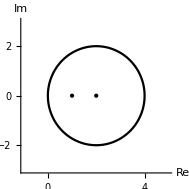

Из рисунка видно, что обе точки лежат внутри контура С.

Найдем интеграл по первой теореме вычетов.

```mathematica
int=2π ⅈ Sum[Residue[f[z],{z,sol[[i]]}],{i,1,Length[sol]}]
```

2 ⅈ π

2) Воспользуемся написанной нами в главе 1 параграфе 4 программой integrateC[z,f[z],a,b]:

```mathematica
integrateC[z,f[z],2,2]
```

2 ⅈ π

Получили тот же самый ответ.

3) Применим новый подход с использованием вычетов. Для этого воспользуемся программой, написанной в предыдущем разделе, residueK[z,f[z],a,b]. Она находит полюса и вычеты в них:

```mathematica
res=residueK[z,f[z],2,2]
```

{{1,-1},{2,2}}

Напомним, что элемент данного множество имеет вид: {z_k,res[f(z),z_k]}

Теперь, для того чтобы найти значение интеграла, воспользуемся первой теоремой о вычетах (6):

```mathematica
int=2I Pi Sum[res[[i,2]],{i,1,Length[res]}]
```

2 ⅈ π

С использованием изложенных выше способов читателю рекомендуется решить задания №№ 12.435-449 самостоятельно.

##### Общий алгоритм

Составим новый программный модуль, взамен старого integrateC[z,f[z],a,b], который будет иметь те же входные параметры, но использовать первую теорему о вычетах:

```mathematica
integrateR[z_,func_,a_,b_]:=Module[{sol},
sol=z/.Solve[Abs[z-a]<b&&func^-1==0,z]//DeleteDuplicates;
2 I Pi Sum[Residue[func,{z,sol[[i]]}],{i,1,Length[sol]}]]
```

Продемонстрируем пример работы:

##### Пример №12.433

```mathematica
-integrateR[z,1/(z^4+1),1,1]//Simplify
```

(ⅈ π)/(√2)

##### Пример №12.436

```mathematica
integrateR[z,Sin[z]/(z^2+9),0,4]
```

2/3 ⅈ π Sinh[3]

##### Пример №12.441

```mathematica
integrateR[z,(z+1)/(Exp[z]+1),0,4]//Simplify
```

-4 ⅈ π

##### Пример №12.437

Используя теоремы о вычетах, вычислить следующий интеграл:

∮ⅆz/((z-a)^n(z-b)^n), C={ z | |z|=1}, n ∈ℕ, 0≤ |a|<1< |b|

Из условий видно, что a - полюс n-ого порядка, который лежит внутри контура С.

Зададим функцию f(z,n) и попробуем найти вычет в точке а с помощью уже хорошо знакомой нам функции Residue:

```mathematica
f[z_,n_]:=1/((z-a)^n(z-b)^n)
```

```mathematica
Residue[f[z,n],{z,a}]
```

Residue[(-a+z)^-n (-b+z)^-n,{z,a}]

В общем виде результат мы не получили.

Теперь попробуем воспользоваться определением вычета:

res[f(z),z_0]=1/((n-1)!)lim_(z→z_0) ⅆ^(n-1)/(ⅆ z^(n-1))[(z-z_0)^n f(z)]

Зададим вычет, как функцию от n:

```mathematica
res1[n_]:=1/((n-1)!)Limit[D[(z-a)^n f[z,n],{z,n-1}],z->a]
```

```mathematica
res1[n]
```

Limit[∂_{z,-1+n} (-b+z)^-n,z→a]/((-1+n)!)

Результат в общем виде мы снова не получили. Зато можем увидеть, как зависит вычет от n:

```mathematica
Table[res1[i],{i,1,5}]
```

{1/(a-b),-2/(a-b)^3,6/(a-b)^5,-20/(a-b)^7,70/(a-b)^9}

Из определения вычета видно:

res[f(z),a]=1/((n-1)!)lim_(z→a) ⅆ^(n-1)/(ⅆ z^(n-1))[1/(z-b)^n]

Запишем:

ⅆ^(n-1)/(ⅆ z^(n-1))[1/(z-b)^k]=(-1)^(n-1)(k(k+1)...(k+n-2))/(z-b)^(k+n-1)=(-1)^(n-1)(n(n+1)...(2n-2))/(z-b)^(2n-1)

Значит:

res[f(z),a]=(-1)^(n-1)/((n-1)!)(n(n+1)...(2n-2))/(a-b)^(2n-1)

И тогда:

∮ⅆz/((z-a)^n(z-b)^n)=2π ⅈ(-1)^(n-1)/((n-1)!)(n(n+1)...(2n-2))/(a-b)^(2n-1) ,n ∈ℕ, 0≤ |a|<1< |b|

##### Пример №12.438

Изменим условия предыдущей задачи на:

0≤ |a|< |b|<1

Тогда ввиду симметрии задачи:

res[f(z),b]=(-1)^(n-1)/((n-1)!)(n(n+1)...(2n-2))/(b-a)^(2n-1)

∮ⅆz/((z-a)^n(z-b)^n)=2π ⅈ((-1)^(n-1)/((n-1)!)(n(n+1)...(2n-2))/(a-b)^(2n-1)+(-1)^(n-1)/((n-1)!)(n(n+1)...(2n-2))/(b-a)^(2n-1))=((-1)^(n-1)/((n-1)!)(n(n+1)...(2n-2))/((-1)^(2n-1)(b-a)^(2n-1))+(-1)^(n-1)/((n-1)!)(n(n+1)...(2n-2))/(b-a)^(2n-1))=(-(-1)^(n-1)/((n-1)!)(n(n+1)...(2n-2))/(b-a)^(2n-1)+(-1)^(n-1)/((n-1)!)(n(n+1)...(2n-2))/(b-a)^(2n-1))=0

Следовательно:

∮ⅆz/((z-a)^n(z-b)^n)=0, n ∈ℕ, 0≤ |a|< |b|<1

### 6.3. Применение вычетов к вычислению определенных интегралов.

I. Интегралы вида:

∫_0^(2π) R(sin(x),cos(x))ⅆx

где R- символ рациональной функции, с помощью замены вида z=e^(ⅈ x)приводятся к контурным интегралам от рациональных относительно z функций.

##### Пример №14.450

Используя метод описанный выше, вычислить определенный интеграл:

∫_0^(2π) 1/(a+b cos(x))^2 ⅆx, a>b>0

Запишем функцию:

```mathematica
f[x_]:=1/(a+b Cos[x])^2
```

Мы конечно же можем  вычислить данный интеграл напрямую:

```mathematica
Assuming[0<b&&a>b&&x∈Reals,Integrate[f[x],{x,0,2 Pi}]]//Timing
```

{7.95605,(2 a π)/((a^2-b^2)^(3/2))}

но на вычисление такого простого интеграла “в лоб” Mathematica затрачивает целых 8 секунд, значит на более сложные интегралы времени уйдет еще больше, так что попробуем упростить задачу заменой описанной выше.

Произведем замену:

ⅇ^(ⅈ x)=z,ⅆx=ⅆz/(ⅈ z)

Тогда получим:

```mathematica
Simplify[TrigToExp[f[x]]*1/(I z)/.<|E^(I x)-> z,E^(-I x)->1/z|>]
```

-(4 ⅈ z)/((b+2 a z+b z^2)^2)

Напомним: функция TrigToExp записывает тригонометрические функции через экспоненциальные, множитель 1/(ⅈ z) следует из (11).

Запишем функцию f_1(z):

```mathematica
f1[z_]:=-(4 I z)/((b+2 a z+b z^2)^2)
```

Найдем полюса из уравнения (f_1(z))^-1=0 при условии, что |z_k|<1, а также a>b, b>0

```mathematica
sol=z/.DeleteDuplicates[Solve[a>b&&b>0&&Abs[z]<1&&f1[z]^-1==0,z]]//Simplify
```

{ConditionalExpression[√(-1+a^2/b^2)-a/b,b>0&&a>b]}

Получили один полюс:

```mathematica
z1=√(-1+a^2/b^2)-a/b;
```

Теперь воспользовавшись первой теоремой о вычетах найдем значение интеграла и время, за которое он вычисляется:

```mathematica
int=2ⅈ π Residue[f1[z],{z,z1}]//Timing
```

{0.0156001,-(2 a π)/(√(-1+a^2/b^2) b (-a^2+b^2))}

Теперь осталось преобразовать ответ, чтобы убедиться, что он совпадает с ответом полученным “в лоб”:

```mathematica
Simplify[int[[2]],a>b&&b>0]
```

(2 a π)/((a^2-b^2)^(3/2))

Мы получили тот же ответ, но за значительно меньший промежуток времени.

Окончательный ответ:

∫_0^(2π) 1/(a+b cos(x))^2 ⅆx=(2 a π)/((a^2-b^2)^(3/2))

Данным алгоритмом можно считать любые интегралы вида:

∫_0^(2π) R(sin(x),cos(x))ⅆx

Остальные номера, №№12.450-455, рекомендуются к самостоятельному выполнению ввиду своего однообразия.

II. Интегралы вида:

∫_(-∞)^∞ f(x)ⅆx

где f(x) - функция непрерывная на  (-∞;∞), аналитическая в верхней полуплоскости, за исключением конечного числа особых точек z1....zn, лежащих в конечной части верхней полуплоскости, вычисляются:

∫_(-∞)^∞ f(x)ⅆx=2π ⅈ∑_(i=1)^n res(f(z), z_i)

##### Пример №12.461

Вычислить интеграл, используя описанный выше способ:

∫_(-∞)^∞ (x^4+1)/(x^6+1)ⅆx

Зададим функцию

```mathematica
f[x_]:=(x^4+1)/(x^6+1)
```

Вычислим интеграл с помощью функции Integrate и измерим время.

```mathematica
Integrate[f[x],{x,-Infinity,Infinity}]//Timing
```

{0.202801,(4 π)/3}

Сравним  время, затрачиваемое на вычисление данного интеграла “в лоб”, с временем, требуемым для решения данной задачи способом описанным выше.

Для этого найдем все полюса, лежащие в верхней полуплоскости ( Im[z]>0):

```mathematica
sol=z/.Solve[Im[z]>0&&f[z]^-1==0,z]
```

{ⅈ,(-1)^(1/6),(-1)^(5/6)}

Изобразим их на комплексной плоскости:

```mathematica
Graphics[{PointSize[Large],Point[ReIm[sol]]},Axes->True,PlotRange->{{-1,1},{0,2}},AxesLabel->{Re,Im}]
```

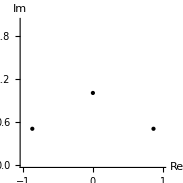

Теперь найдем значение интеграла согласно (12):

```mathematica
int=2 ⅈ π Sum[Residue[f[z],{z,sol[[i]]}],{i,1,Length[sol]}]//ComplexExpand//Timing
```

{0.,(4 π)/3}

Получили тот же ответ, но время, затраченное на его вычисление, пренебрежимо мало.

Итак, имеем:

∫_(-∞)^∞ f(x)ⅆx=(4 π)/3

Способы, описанные выше, можно применить ко всем задачам №№12.450-470, что и рекомендуется сделать самостоятельно.

### 6.4. Разложение в ряд Лорана по методу вычетов

Вычет функции в точке равен коэффициенту c_-1 разложения в ряд Лорана, значит, если идти в обратном направлении, можно найти этот коэффициент. Воспользуемся этим для того, чтобы написать модуль разложения функции в ряд Лорана. Рассмотрим пример.

##### Пример №12.357

Найти все разложения указанной функции в ряд Лорана по степеням z-z_0 и установить области сходимости:

f(z)=(z+1)/(z^2-3z+2), z_0=1

Запишем функцию:

```mathematica
f[z_]:=(z+1)/(z^2-3z+2)
```

Получим множество особых точек:

```mathematica
sol=z/.Solve[z^2-3z+2==0,z]
```

{1,2}

Точка z_0 является полюсом первого порядка. Для того чтобы вычислить коэффициент Лорана, нам нужно вычислить интеграл:

c_n=1/(2π ⅈ)∮_(|z-1|=r') (f(z))/(z-1)^(n+1)ⅆz,     где 0<r'<1

Вычет по определению равен:

res[f(z),1]=c_-1=1/(2 π ⅈ)∮_(|z-z_0|=r') f(z)ⅆz

Отсюда следует, что если мы будем применять функцию Residue к функции f(z)/(z-z_0)^(n+1) , то будем получать n-ый коэффициент Лорана:

res[(f(z))/(z-1)^(n+1),1]=c_n=1/(2 π ⅈ)∮_(|z-z_0|=r') (f(z))/(z-1)^(n+1)ⅆz

Итак, запишем функцию n-ого коэффициента при разложении вблизи точки z_0:

```mathematica
c[n_]:=Residue[f[z]/(z-1)^(n+1),{z,1}]
```

Получим разложение в ряд:

```mathematica
Sum[c[n](z-1)^n,{n,-5,5}]
```

-3-2/(-1+z)-3 (-1+z)-3 (-1+z)^2-3 (-1+z)^3-3 (-1+z)^4-3 (-1+z)^5

Сравним ответ с результатом работы функции loranO:

```mathematica
loranO[z,f[z],1,1/2,5]
```

-3-2/(-1+z)-3 (-1+z)-3 (-1+z)^2-3 (-1+z)^3-3 (-1+z)^4-3 (-1+z)^5

и с результатом Series:

```mathematica
Series[f[z],{z,1,5}]
```

-2/(z-1)-3-3 (z-1)-3 (z-1)^2-3 (z-1)^3-3 (z-1)^4-3 (z-1)^5+O[z-1]^6

Во всех случаях получили одинаковый ответ.

Теперь получим коэффициент разложения в кольце с радиусом r>1:

c_n=1/(2π ⅈ)∮_(|z-1|=R) (f(z))/(z-1)^(n+1)ⅆz,     где R>1

Согласно первой теореме вычетов этот интеграл будет равен:

1/(2π ⅈ)∮_(|z-1|=R) (f(z))/(z-1)^(n+1)ⅆz=∑_(k=1)^N res[(f(z))/(z-1)^(n+1);z_k]

где z_k- полюса, охватываемые контуром интегрирования.

Отсюда,  n-ый коэффициент будем искать по формуле:

c_n=res[(f(z))/(z-1)^(n+1),1]+∑_(k=1)^N res[(f(z))/(z-1)^(n+1);z_k],     где R>1

где z_k- полюса, охватываемые контуром интегрирования R, за исключением полюса z_0.

Итак, первое слагаемое у нас уже вычислено, осталось найти второе:

```mathematica
c1[n_]:=Residue[f[z]/(z-1)^(n+1),{z,2}]
```

Теперь чтобы получить разложение в ряд Лорана в кольце R>1:

```mathematica
Sum[(c[n]+c1[n])(z-1)^n,{n,-5,5}]
```

3/(-1+z)^5+3/(-1+z)^4+3/(-1+z)^3+3/(-1+z)^2+1/(-1+z)

Сравним ответы:

```mathematica
loranO[z,f[z],1,3,5]
```

3/(-1+z)^5+3/(-1+z)^4+3/(-1+z)^3+3/(-1+z)^2+1/(-1+z)

Так как функции Series и SeriesCoefficient работают быстрее всего, то рациональнее по возможности использовать их. Коэффициент c_n вблизи точки z_0 оптимальнее искать именно с помощью функции SeriesCoefficient.

Соберем всё это в единый модуль:

```mathematica
loranR[expr_,{z_,z0_,k_},r_]:=Module[{sol,c,c1},
sol=z/.Solve[0<Abs[z-z0]<r&&Denominator[Simplify[TrigToExp[expr]]]==0,z];
c[n_]:=Evaluate[SeriesCoefficient[expr,{z,z0,n}]];
If[Length[sol]≠0,
sol=DeleteDuplicates[sol];
c1[n_]:=Sum[Residue[expr/(z-z0)^(n+1),{z,sol[[i]]}],{i,1,Length[sol]}],c1[n_]:=0;];
Sum[(c1[n]+c[n])(z-z0)^n,{n,-k,k}]]
```

##### Пример №12.364

```mathematica
loranR[z/((z^2+1)^2),{z,I,5},1/2]
```

-ⅈ/16-ⅈ/(4 (-ⅈ+z)^2)+1/16 (-ⅈ+z)+3/64 ⅈ (-ⅈ+z)^2-1/32 (-ⅈ+z)^3-5/256 ⅈ (-ⅈ+z)^4+3/256 (-ⅈ+z)^5

```mathematica
loranR[z/((z^2+1)^2),{z,I,8},3]
```

-(112 ⅈ)/(-ⅈ+z)^8+48/(-ⅈ+z)^7+(20 ⅈ)/(-ⅈ+z)^6-8/(-ⅈ+z)^5-(3 ⅈ)/(-ⅈ+z)^4+1/(-ⅈ+z)^3

##### Пример №12.375

```mathematica
loranR[1/((z^2-4)(z^2-1)),{z,0,8},1/2]
```

1/4+(5 z^2)/16+(21 z^4)/64+(85 z^6)/256+(341 z^8)/1024

```mathematica
loranR[1/((z^2-4)(z^2-1)),{z,I,5},3/2]
```

-1/15+2/(3 (-ⅈ+z)^4)+(2 ⅈ)/(3 (-ⅈ+z)^3)-1/(3 (-ⅈ+z)^2)-2/75 ⅈ (-ⅈ+z)-1/375 (-ⅈ+z)^2-4/625 ⅈ (-ⅈ+z)^3+(19 (-ⅈ+z)^4)/9375-(22 ⅈ (-ⅈ+z)^5)/46875

```mathematica
loranR[1/((z^2-4)(z^2-1)),{z,I,8},5/2]
```

-49/(-ⅈ+z)^8-(10 ⅈ)/(-ⅈ+z)^7-5/(-ⅈ+z)^6-(4 ⅈ)/(-ⅈ+z)^5+1/(-ⅈ+z)^4

Сравним скорость работы этой функции и функции loranO при больших степенях разложения:

```mathematica
Timing[loranR[z/((z^2+1)^2),{z,I,500},5/2];]
```

{0.561604,Null}

```mathematica
Timing[loranO[z,z/((z^2+1)^2),I,5/2,500];]
```

{7.17605,Null}

Так как функция loranR работает быстрее, предпочтение в использовании будем отдавать именно ей.

## §7. Ряды Фурье. Интеграл Фурье.

### 7.1. Разложение функций в тригонометрические ряды Фурье.

Тригонометрическая система функций

1,cos x, sin x, cos 2x, sin 2x,..., cos n x,sin n x,...

является ортогональной на отрезке [-π,π] (как, впрочем, и на всяком отрезке длины 2π), т.е. интеграл по этому отрезку от произведения любых двух различных функций этой системы равен нулю.

Если f(x) ∈L(-π,π) (т.е. ∫_-π^π |f(x)|ⅆx<+∞), то существуют числа

a_n=1/π∫_-π^π f(x)cos(n x)ⅆx    n=0,1,2,...

b_n=1/π∫_-π^π f(x)sin(n x)ⅆx, n=1,2,...

называемые коэффициентами Фурье функции f(x).

Ряд

S(x)=a_0/2+∑_(n=1)^∞ (a_n cos(n x)+b_n sin(n x))

называется рядом Фурье функции f(x).

Члены ряда (1) можно записать в виде гармоник

a_n cos(n x)+b_n sin(n x)=A_n cos(n x-ϕ_n)

с амплитудой A_n=√(a_n^2+b_n^2) , частотой ω_n=n и фазой ϕ_n=arctg b_n/a_n.

Для функции f(x) такой, что f^2(x)∈L(-π,π), справедливо равенство Парсеваля

1/π∫_-π^π f^2(x)ⅆx=a_0^2/2+∑_(n=1)^∞ (a_n^2+b_n^2)

Если же f(x) ∈L(-l,l) , то коэффициенты Фурье записываются в виде:

a_0=1/l∫_-l^l f(x)ⅆx

a_n=1/l∫_-l^l f(x)cos(π/l n x)ⅆx

b_n=1/l∫_-l^l f(x)sin(π/l n x)ⅆx

а ряд Фурье - в виде

S(x)=a_0/2+∑_(n=1)^∞ (a_n cos(π/l n x)+b_n sin(π/l n x))

Суммы рядов (1) и (5) имеют периоды соответственно 2π и 2l.

Функция f(x) называется кусочно гладкой на отрезке [a;b], если сама функция f(x) и ее производная f'(x) имеют на [a;b] конечное число точек разрыва 1-ого рода.

Т е о р е м а. Если периодическая функция f(x) с периодом 2l кусочно гладка на отрезке [-l;l], то ряд Фурье (5) сходится к значению f(x) в каждой ее точке непрерывности и к значению  (f(x+0)+f(x-0))/2 в точке разрыва, т.е.

1/2(f(x+0)+f(x-0))=a_0/2+∑_(n=1)^∞ (a_n cos(π/l n x)+b_n sin(π/l n x))

Если, дополнительно, f(x) непрерывна на всей оси, то ряд (5) сходится к f(x) равномерно.

Если на полуоткрытом интервале длины 2l, т.е. на интервале вида [a,a+2l) или (a,a+2l], определена какая-нибудь функция, то она может быть (единственным способом) продолжена на всю числовую прямую так, что получится функция с периодом 2l.

Отсюда следует, что если f(x) имеет на [-l,l] не более конечного числа точек разрыва и абсолютно интегрируема на этом сегменте, то она представима рядом Фурье (5).

##### Пример №12.480

Разложить периодическую функцию с периодом 2l функцию в ряд Фурье, построить график.

f(x)=Piecewise[{{1, при 0<x<π}, {0, при -π<x<0}}]

Запишем исходную кусочно-заданную функцию и построим ее график:

```mathematica
f[x_]:=Piecewise[{{1,0<x<Pi},{0,-Pi<x<0}}]
Plot[f[x],{x,-Pi,Pi},PlotRange->{-0.5,1.5}]
```

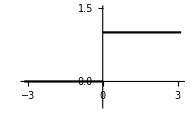

Запишем выражения для коэффициентов Фурье по формулам (2), (3), (4)

Так как функция обращается в ноль при x<0, интегрирование ведем в пределах от 0 до π.

Коэффициент a_0 вычисляется следующим образом:

```mathematica
a0=1/π Integrate[f[x],{x,0,Pi}]
```

1

Коэффициент a_n:

```mathematica
an=1/π Integrate[f[x]Cos[n x],{x,0,Pi}]
```

Sin[n π]/(n π)

При любых n a_n=0, но a_0=1

Коэффициент b_n:

```mathematica
bn=1/π Integrate[f[x]Sin[n x],{x,0,Pi}]
```

(1-Cos[n π])/(n π)

Получили, что коэффициент b_n:

b_n=Piecewise[{{2/((2k+1) π), при n=2k+1}, {0, при n=2k}}]

Запишем ряд Фурье:

f(x)=1/2+∑_(k=0)^∞ (2sin((2k+1)x))/((2k+1)π)

```mathematica
fu[x_,n_]:=1/2+2/π Sum[Sin[(2k+1)x]/(2k+1),{k,0,n}]
```

Получим выражение ряда Фурье до 4-ого члена:

```mathematica
fu[x,4]//Expand
```

1/2+(2 Sin[x])/π+(2 Sin[3 x])/(3 π)+(2 Sin[5 x])/(5 π)+(2 Sin[7 x])/(7 π)+(2 Sin[9 x])/(9 π)

Изобразим графики исходной функции и ряда Фурье до 4ого и до 10ого члена.

```mathematica
Row[{Plot[{fu[x,4],f[x]},{x,-Pi,Pi},ImageSize->300],Plot[{fu[x,10],f[x]},{x,-Pi,Pi},ImageSize->300] }]
```

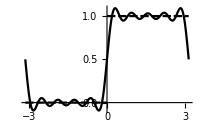
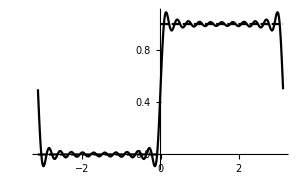

Из графиков видно, что чем больше порядок разложения, тем точнее ряд аппроксимирует функцию.

В данной задаче было показано, как на основе формул для определения коэффициентов Фурье разложить функцию в ряд Фурье.

##### Пример №12.487

Разложить периодическую функцию с периодом 2l функцию в ряд Фурье, построить график.

f(x)=2x ,       0<x<1, 2l=1

Определим заданную функцию, и построим ее график:

```mathematica
f[x_]:=2x
l=1/2;
Plot[f[x],{x,0,1}]
```

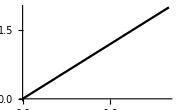

Теперь запишем функции для коэффициентов Фурье по формулам (2), (3), (4):

Так как в формуле (3) при n=0 косинус обращается в единицу, то записывать отдельное выражение для коэффициента a_0 смысла нет.

```mathematica
a[n_]:=Integrate[1/l f[x]Cos[Pi n x/l],{x,0,1}]
b[n_]:=Integrate[1/l f[x] Sin[Pi n x/l],{x,0,1}]
```

Теперь запишем функцию тригонометрического ряда Фурье:

```mathematica
fu[x_,k_]:=a[0]/2+Sum[a[n]Cos[Pi/l n x]+b[n]Sin[Pi/l n x],{n,1,k}]
```

Выведем выражение для ряда до 5ого члена и построим его график:

```mathematica
fu[x,5]
Plot[{Evaluate@fu[x,5],f[x]},{x,0,1}]
```

1-(2 Sin[2 π x])/π-Sin[4 π x]/π-(2 Sin[6 π x])/(3 π)-Sin[8 π x]/(2 π)-(2 Sin[10 π x])/(5 π)

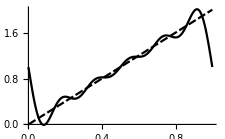

Чтобы оценить верность полученного выражения, найдем сумму ряда:

```mathematica
fu[x,Infinity]
```

1+(ⅈ (-Log[1-ⅇ^(2 ⅈ π x)]+Log[ⅇ^(-2 ⅈ π x) (-1+ⅇ^(2 ⅈ π x))]))/π

Построим график полученной функции:

```mathematica
Plot[{f[x],Evaluate@fu[x,Infinity]},{x,0,1}]
```

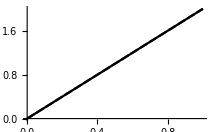

Графики функций совпали, следовательно, как и предполагалось, ряд сходится к функции.

### 7.2. Особенности разложения в ряд Фурье четных и нечетных функций.

Если функцию обладает какой-либо симметрией, то техника разложения в ряд Фурье упрощается.

В случае, если f(x) - четная функция с периодом 2l, то все коэффициенты Фурье b_n равны 0 и, следовательно, в ряде Фурье нет членов с синусами. Тогда получим ряд:

S(x)=a_0/2+∑_(n=1)^∞ a_n cos(π/l n x)

где

a_0=2/l∫_0^l f(x)ⅆx

a_n=2/l∫_0^l f(x)cos(π/l n x)ⅆx

Аналогично в случае, если f(x) - нечетная функция, то все коэффициенты Фурье a_n равны 0 и, следовательно, в ряде Фурье нет членов с косинусами. Тогда получим ряд:

S(x)=∑_(n=1)^∞ b_n sin(π/l n x)

где

b_n=2/l∫_0^l f(x)sin(π/l n x)ⅆx

##### Пример №12.482

Разложить в ряд Фурье функцию:

f(x)=|x|,  -1<x<1, l=1

Запишем заданную функцию:

```mathematica
f[x_]:=Abs[x]
```

Функция четная, значит в разложении будут отсутствовать члены с синусами. Запишем теперь выражение для коэффициента a_n:

```mathematica
a[n_]:=Integrate[2 f[x] Cos[Pi n x],{x,0,1}]
```

Зададим функцию ряда:

```mathematica
fu[x_,k_]:=a[0]/2+Sum[a[n]Cos[Pi n x],{n,1,k}]
```

Выведем полученный ряд до 6ого члена и построим его график:

```mathematica
fu[x,6]
Plot[{f[x],Evaluate@fu[x,6]},{x,-1,1}]
```

1/2-(4 Cos[π x])/π^2-(4 Cos[3 π x])/(9 π^2)-(4 Cos[5 π x])/(25 π^2)

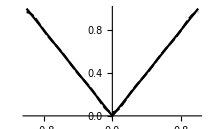

Из графика заключаем, что ряд сходится к функции.

##### Пример №12.493

Доопределяя необходимым образом заданную в промежутке функцию до периодической, получить для нее: а) ряд Фурье по косинусам; б) ряд Фурье по синусам.

f(x)=e^x, 0<x<ln 2

Для того чтобы получить ряд Фурье по косинусам, необходимо чтобы функция была чётной. Функция e^(|x|) удовлетворяет данному требованию. Запишем и изобразим эту функцию:

```mathematica
f[x_]:=Exp[Abs[x]]
Plot[f[x],{x,-Log[2],Log[2]}]
```

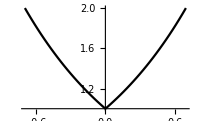

Теперь получим выражение для коэффициента Фурье и запишем ряд:

```mathematica
a[n_]:=Integrate[2/Log[2] f[x]Cos[Pi/Log[2] n x],{x,0,Log[2]}]
fu[x_,k_]:=a[0]/2+Sum[a[n]Cos[Pi/Log[2] n x],{n,1,k}]
```

Изобразим полученный ряд:

```mathematica
fu[x,5]
Plot[{f[x],Evaluate@fu[x,5]},{x,-Log[2],Log[2]}]
```

1/Log[2]-(6 Cos[(π x)/Log[2]] Log[2])/(π^2+Log[2]^2)-(6 Cos[(3 π x)/Log[2]] Log[2])/(9 π^2+Log[2]^2)-(6 Cos[(5 π x)/Log[2]] Log[2])/(25 π^2+Log[2]^2)+(Cos[(2 π x)/Log[2]] Log[4])/(4 π^2+Log[2]^2)+(Cos[(4 π x)/Log[2]] Log[4])/(16 π^2+Log[2]^2)

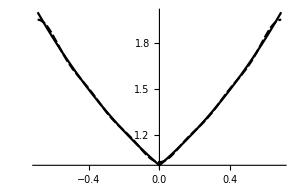

Теперь, для того чтобы получить разложение Фурье по синусам, доопределим исходную функцию до нечетной следующим образом:

f(x)=Piecewise[{{e^x, 0<x<ln 2}, {-e^-x, -ln 2<x<0}}]

Запишем и построим полученную функцию:

```mathematica
f[x_]:=Piecewise[{{Exp[x],Log[2]>x>0},{-Exp[-x],-Log[2]<x<0}}]
Plot[f[x],{x,-Log[2],Log[2]}]
```

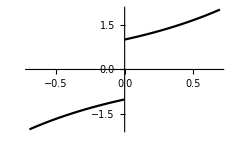

Запишем выражения для коэффициента b_n и ряда:

```mathematica
b[n_]:=Integrate[2/Log[2] f[x]Sin[Pi/Log[2] n x],{x,0,Log[2]}]
fu[x_,k_]:=Sum[b[n]Sin[Pi/Log[2] n x],{n,1,k}]
```

Получим разложение функции до 6ого члена и построим его график:

```mathematica
fu[x,6]
Plot[{f[x],Evaluate@fu[x,12]},{x,-Log[2],Log[2]}]
```

(6 π Sin[(π x)/Log[2]])/(π^2+Log[2]^2)-(4 π Sin[(2 π x)/Log[2]])/(4 π^2+Log[2]^2)+(18 π Sin[(3 π x)/Log[2]])/(9 π^2+Log[2]^2)-(8 π Sin[(4 π x)/Log[2]])/(16 π^2+Log[2]^2)+(30 π Sin[(5 π x)/Log[2]])/(25 π^2+Log[2]^2)-(12 π Sin[(6 π x)/Log[2]])/(36 π^2+Log[2]^2)

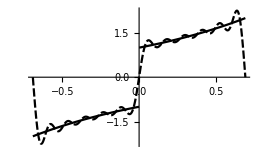

В точке разрыва значение ряда S(0) будет равно:

S(0)=(f(+0)+f(-0))/2

##### Программный модуль

Проанализировав последовательность действий в общем случае, напишем простую обучающую программу, которая будет раскладывать функцию в ряд Фурье на заданном интервале [h;g] с полупериодом l=(g-h)/2:

```mathematica
fourier[x_,func_,h_,g_,k_]:=Module[{a,b,l},
l=(g-h)/2;
a[n_]:=Integrate[1/l func Cos[Pi n x/l],{x,h,g}];
b[n_]:=Integrate[1/l func  Sin[Pi n x/l],{x,h,g}];
a[0]/2+Sum[a[n]Cos[Pi/l n x]+b[n]Sin[Pi/l n x],{n,1,k}]]
```

Проведем графическую проверку полученного модуля:

##### Пример №12.483

Разложить в ряд Фурье функцию:

f(x)=|cos(x)|,  -π<x<π, l=π

Зададим функцию ряда через написанный нами модуль:

```mathematica
fu[x_,k_]:=fourier[x,Abs[Cos[x]],-Pi,Pi,k]
```

Теперь выведем разложение до 8-ого члена и построим график:

```mathematica
fu[x,8]
Plot[{Abs[Cos[x]],Evaluate@fu[x,8]},{x,-Pi,Pi}]
```

2/π+(4 Cos[2 x])/(3 π)-(4 Cos[4 x])/(15 π)+(4 Cos[6 x])/(35 π)-(4 Cos[8 x])/(63 π)

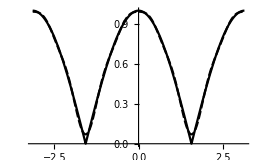

При увеличении порядка разложения ряд будет сходиться к функции.

##### Пример №12.488

Разложить в ряд Фурье функцию:

f(x)=10-x,  5<x<15, l=5

```mathematica
fu[x_,k_]:=fourier[x,10-x,5,15,k]
```

```mathematica
fu[x,8]
Plot[{10-x,Evaluate@fu[x,8]},{x,5,15}]
```

-(10 Sin[(π x)/5])/π+(5 Sin[(2 π x)/5])/π-(10 Sin[(3 π x)/5])/(3 π)+(5 Sin[(4 π x)/5])/(2 π)-(2 Sin[π x])/π+(5 Sin[(6 π x)/5])/(3 π)-(10 Sin[(7 π x)/5])/(7 π)+(5 Sin[(8 π x)/5])/(4 π)

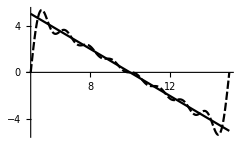

Разобрав два примера, будем считать, что написанный модуль проверку прошел.

### 7.3. Ряд Фурье в комплексной форме.

Применим тождества Эйлера для косинуса и синуса ряда (1):

S(t)=a_0/2+∑_(n=1)^∞ (a_n cos(n t)+b_n sin(n t))=a_0/2+∑_(n=1)^∞ (a_n(e^(i n t)+e^(- i n t))/2+b_n(e^(i n t)- e^(-i n t))/(2i))=
=a_0/2+∑_(n=1)^∞ (a_n(e^(i n t)+e^(- i n t))/2-i b_n(e^(i n t)- e^(-i n t))/2)=a_0/2+∑_(n=1)^∞ ((a_n-i b_n)/2 e^(i n t)+(a_n+i b_n)/2 e^(-i n t))

Введем коэффициенты a_n и b_n  с отрицательными номерами:

a_-n=a_n
b_-n=b_n

Для которых также справедливы формулы:

a_-n=1/π∫_-π^π f(t)cos(-n t)ⅆt=1/π∫_-π^π f(t)cos(n t)ⅆt=a_n
b_-n=1/π∫_-π^π f(t)sin(-n t)ⅆt=-1/π∫_-π^π f(t)sin(n t )ⅆt=-b_n

Продолжим преобразование:

f(t)=a_0/2+∑_(n=1)^∞ (a_n-i b_n)/2 e^(i n t)+∑_(n=-∞)^-1 (a_n-i b_n)/2 e^(i n t)=∑_(n=-∞)^∞ (a_n-i b_n)/2 e^(i n t)

Обозначим:

c_n=(a_n-i b_n)/2=1/(2π)∫_-π^π f(t)cos(n t)ⅆt-i 1/(2π)∫_-π^π f(t)sin(n t)ⅆt=1/(2π)∫_-π^π f(t)e^(-n t)ⅆt

Итак, в комплексной форме ряд Фурье для функции с произвольным полупериодом l записывается:

f(t)=∑_(n=-∞)^∞ c_n ⅇ^((ⅈ n π x)/l)

c_n=1/(2l)∫_-l^l f(t)ⅇ^(-(ⅈ n π t)/l)ⅆt

##### Пример №12.484

Представить функцию в виде ряда Фурье в комплексной форме:

f(t)=t^2, -π<t<π, l=π

Запишем функцию:

```mathematica
f[t_]:=t^2
```

Используя формулу (13), запишем коэффициент c_n:

```mathematica
c[n_]:=Integrate[1/(2Pi)f[t] Exp[-I n t],{t,-Pi,Pi}]
```

Запишем функцию ряда Фурье до k-ого порядка:

```mathematica
fu[t_,k_]:=Sum[c[n]Exp[I n t],{n,-k,k}]
```

Получим выражение ряда до 4-ого порядка:

```mathematica
fu[t,4]
```

-2 ⅇ^(-ⅈ t)-2 ⅇ^(ⅈ t)+1/2 ⅇ^(-2 ⅈ t)+1/2 ⅇ^(2 ⅈ t)-2/9 ⅇ^(-3 ⅈ t)-2/9 ⅇ^(3 ⅈ t)+1/8 ⅇ^(-4 ⅈ t)+1/8 ⅇ^(4 ⅈ t)+π^2/3

Сравним данный результат, преобразовав его при помощи функции ExpToTrig, с тем, что бы у нас получилось, если бы мы воспользовались модулем fourier:

```mathematica
fourier[t,f[t],-Pi,Pi,4]
fu[t,4]//ExpToTrig
```

π^2/3-4 Cos[t]+Cos[2 t]-4/9 Cos[3 t]+1/4 Cos[4 t]

π^2/3-4 Cos[t]+Cos[2 t]-4/9 Cos[3 t]+1/4 Cos[4 t]

Как и ожидалось, ответы совпадают.

Построим график, чтобы убедиться, что ряд сходится к исходной функции:

```mathematica
Plot[{f[t],Evaluate@fu[t,4]},{t,-Pi,Pi}]
```

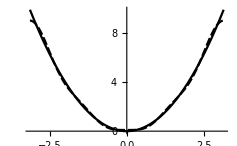

##### Программный модуль

Подобно модулю разложения в тригонометрический ряд составим модуль разложения в ряд Фурье в комплексной форме:

```mathematica
fourierC[t_,func_,h_,g_,k_]:=Module[{c,l},
l=(g-h)/2;
c[n_]:=1/(2l)Integrate[func Exp[- I Pi/l n t],{t,h,g}];
Sum[c[n]Exp[I Pi/l n t],{n,-k,k}]]
```

##### Пример №12.486

Представить функцию в виде ряда Фурье в комплексной форме:

f(t)=|sin(t)|, -π<t<π, l=π

Выведем результат работы функции fourierC и построим графики исходной функции и полученного ряда:

```mathematica
fourierC[t,Abs[Sin[t]],-Pi,Pi,4]
Plot[{Abs[Sin[t]],Evaluate@fourierC[t,Abs[Sin[t]],-Pi,Pi,4]},{t,-Pi,Pi}]
```

2/π-(2 ⅇ^(-2 ⅈ t))/(3 π)-(2 ⅇ^(2 ⅈ t))/(3 π)-(2 ⅇ^(-4 ⅈ t))/(15 π)-(2 ⅇ^(4 ⅈ t))/(15 π)

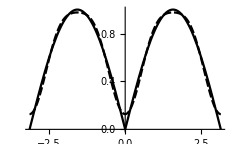

Будем считать, что проверка прошла успешно.

### 7.4. Системные функции разложения в ряд Фурье.

Mathematica имеет встроенные функции разложения в ряд Фурье. Рассмотрим на примере:

##### Пример №12.484

Разложить функцию в ряд Фурье периода l:

f(x)=x^2, -π<x<π, l=π

Для решения данной задачи воспользуемся встроенной функцией FourierSeries, имеющей следующую структуру: FourierSeries[expr,t,n] , где expr - выражение или функция, которую требуется разложить в ряд Фурье, t - переменная, по которой ведется разложение, n - порядок разложения.

Запишем исходную функцию:

```mathematica
f[x_]:=x^2
```

Теперь получим разложение в ряд до 6ого члена.

```mathematica
FourierSeries[x^2,x,6]
```

-2 ⅇ^(-ⅈ x)-2 ⅇ^(ⅈ x)+1/2 ⅇ^(-2 ⅈ x)+1/2 ⅇ^(2 ⅈ x)-2/9 ⅇ^(-3 ⅈ x)-2/9 ⅇ^(3 ⅈ x)+1/8 ⅇ^(-4 ⅈ x)+1/8 ⅇ^(4 ⅈ x)-2/25 ⅇ^(-5 ⅈ x)-2/25 ⅇ^(5 ⅈ x)+1/18 ⅇ^(-6 ⅈ x)+1/18 ⅇ^(6 ⅈ x)+π^2/3

Как мы видим, по умолчанию Mathematica раскладывает в ряд в комплексной форме. Также мы можем перейти к более привычной для нас, тригонометрической, форме:

```mathematica
FourierSeries[x^2,x,6]//ExpToTrig
```

π^2/3-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x]-4/25 Cos[5 x]+1/9 Cos[6 x]

или же можем просто воспользоваться функцией FourierTrigSeries:

```mathematica
FourierTrigSeries[x^2,x,6]
```

π^2/3+4 (-Cos[x]+1/4 Cos[2 x]-1/9 Cos[3 x]+1/16 Cos[4 x]-1/25 Cos[5 x]+1/36 Cos[6 x])

Как мы видим, функция - четная, а функции синуса в разложении отсутствуют.

Найдем формулу n-ого коэффициента при помощи функции FourierCoefficient:

```mathematica
FourierCoefficient[x^2,x,n]
```

(2 (-1)^n)/n^2

Напоминаем, что это коэффициент разложения в комплексной форме с_n, и он не равен коэффициентам a_n или b_n.

Так же находим и свободный коэффициент:

```mathematica
FourierCoefficient[x^2,x,0]
```

π^2/3

Составим функцию ряда:

```mathematica
fu[x_,n_]:=FourierSeries[t^2,t,n]/.t-> x
```

```mathematica
fu[x,6]//ExpToTrig
```

π^2/3-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x]-4/25 Cos[5 x]+1/9 Cos[6 x]

Покажем графики  исходной функции и ряда Фурье до 5ого порядка:

```mathematica
Plot[{f[x],Evaluate@fu[x,5]},{x,-Pi,Pi}]
```

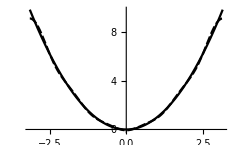

##### Пример №12.496

Доопределяя необходимым образом заданную в промежутке функцию до переодической, получить для нее: а) ряд Фурье по косинусам б) ряд Фурье по синусам.

f(x)=x sin(x), 0<x<π

Так как данная функция - четная, получим выражение ряда в общей форме.

Для этого запишем и построим график заданной функции:

```mathematica
f[x_]:=x Sin[x]
Plot[f[x],{x,-Pi,Pi}]
```

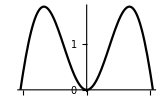

Так как данная функция - четная, в разложении будут отсутствовать члены с синусом. Тогда:

c_n=(a_n-i b_n)/2=(a_n-i 0)/2⇒a_n=2 c_n

Получим выражение для нулевого и n-ого коэффициента:

```mathematica
FourierCoefficient[f[x],x,n]
```

(-1)^(1+n)/(-1+n^2)

Отсюда следует, что

a_n=(2(-1)^(n+1))/(n^2-1)

Найдем значение коэффициента при n=1:

```mathematica
FourierCoefficient[f[x],x,1]
```

-1/4

Теперь можем записать ряд в виде:

f(x)=1-1/2 cos(x)+∑_(n=2)^∞ (2(-1)^(n+1))/(n^2-1)cos(n x)

Ряд Фурье по синусам для исходной функции получим при помощи встроенной опции FourierSinSeries (существует аналогичная опция FourierCosSeries),  она имеет ту же структуру, что и FourierSeries:

```mathematica
FourierSinSeries[f[x],x,8]
```

1/2 π Sin[x]-(16 Sin[2 x])/(9 π)-(32 Sin[4 x])/(225 π)-(48 Sin[6 x])/(1225 π)-(64 Sin[8 x])/(3969 π)

Изобразим график функции и ряда:

```mathematica
Plot[{f[x],Evaluate@FourierSinSeries[f[x],x,8]},{x,-Pi,Pi}]
```

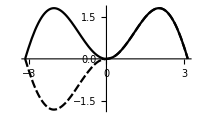

Как видно из графика, исходная функция была доопределена до несимметричной функции, у которой отсутствует косинус в разложении в ряд.

Коэффициент b_n получим при помощи функции FourierSinCoefficient:

```mathematica
FourierSinCoefficient[f[x],x,n]
```

-(4 (1+(-1)^n) n)/((-1+n^2)^2 π)

а также коэффициент b_1:

```mathematica
FourierSinCoefficient[f[x],x,1]
```

π/2

В итоге, ряд записывается в виде:

f(x)=π/2 sin(x)-4/π∑_(n=2)^∞ ((1+(-1)^n) n)/((-1+n^2)^2)sin(n x)

### 7.5. Интеграл Фурье. Преобразование Фурье.

Пусть функция f(x):

1) Абсолютно интегрируема на ℝ, т.е. сходится интеграл: ∫_(-∞)^(+∞) |f(x)|𝕕 x;

2) Кусочно гладкая на каждом конечном отрезке действительной оси.

Тогда справедлива интегральная формула Фурье:

(f(x+0)-f(x-0))/2=1/π∫_0^∞ 𝕕 ω∫_(-∞)^∞ f(t)cosω(x-t)ⅆt

Чтобы показать аналогию интеграла Фурье и ряда Фурье, проведем некоторые преобразования:

f(x)=1/π∫_0^∞ 𝕕 ω∫_(-∞)^∞ f(t)(cos ω t cos ω x + sin ω t sin ω x)ⅆt=
=1/π∫_0^∞ (∫_(-∞)^∞ f(t)cos ω tⅆt )cos ω x +(∫_(-∞)^∞ f(t) sin ω tⅆt )sin ω x 𝕕 ω

Введя обозначения:

A(ω)=∫_(-∞)^∞ f(t)cos ω tⅆt , B(ω)=∫_(-∞)^∞ f(t) sin ω tⅆt

Получаем:

f(x)=1/π∫_0^∞ A(ω)cos ω x +B(ω)sin ω x 𝕕 ω

В этом случае, в отличии от тригонометрического ряда Фурье, частота ω изменяется не дискретно, а непрерывно. И наиболее важным отличием является то, что в виде интеграла Фурье можно представить и непериодическую функцию.

Как и ряд Фурье, интеграл Фурье имеет комплексную форму записи.

Так как внутренний интеграл в выражении (14) функция четная, тогда:

1/π∫_0^∞ 𝕕 ω∫_(-∞)^∞ f(t)cos ω(x-t)ⅆt=1/(2π)∫_(-∞)^∞ 𝕕 ω∫_(-∞)^∞ f(t)cos ω(x-t)ⅆt

Так как:

∫_(-∞)^∞ f(t)sin ω(x-t)ⅆt- нечетная функция от ω, то ⅈ/(2π)∫_(-∞)^∞ 𝕕 ω∫_(-∞)^∞ f(t)sin ω(x-t)ⅆt=0

Тогда:

f(x)=1/(2π)∫_(-∞)^∞ 𝕕 ω∫_(-∞)^∞ f(t)(cos ω(x-t)+ⅈ sin ω(x-t))ⅆt=1/(2π)∫_(-∞)^∞ 𝕕 ω∫_(-∞)^∞ f(t)ⅇ^(ⅈ ω (x-t))ⅆt=

=1/(√(2π))∫_(-∞)^∞ ⅇ^(ⅈ ω x)(1/(√(2π))∫_(-∞)^∞ f(t)ⅇ^(-ⅈ ω t)ⅆt)𝕕 ω

Функция:

S(ω)= 1/(√(2π))∫_(-∞)^∞ f(t)ⅇ^(-ⅈ ω t)ⅆt

Называется прямым преобразованием Фурье функции f(x). Преобразованием Фурье также называют отображение f(x)⟶ S(ω), которое задается формулой (17). Обратное отображение называется обратным преобразованием Фурье, и задается формулой:

f(x)=1/(√(2π))∫_(-∞)^∞ ⅇ^(ⅈ ω x)S(ω) 𝕕 ω

Комплекснозначная функция S(ω) называется также спектральной плотностью функции f(x) и несет в себе значительную информацию о функции f(x).

Если функция f(x) четная, интегральную формулу (18) можно записать так:

f(x)=∫_0^∞ A(ω)cos ω x 𝕕 ω=2/π∫_0^∞ (∫_0^∞ f(t)cos ω tⅆt)cos ω x 𝕕 ω

Обозначим:

f^*( ω)=√(2/π) ∫_0^∞ f(t)cos ω tⅆt

Тогда получим:

f(x)=√(2/π)∫_0^∞ f^*(ω) cos ω x 𝕕 ω

Функция f^*(ω) называется косинус-преобразованием Фурье функции f(x).

Аналогично, если f(x) - нечетная, то можно рассмотреть синус-преобразование:

f_*( ω)=√(2/π) ∫_0^∞ f(t)sin ω tⅆt

f( x)=√(2/π) ∫_0^∞ f_*( ω) sin ω tⅆt

##### Пример №1

Найти преобразование Фурье функции и представить ее интегралом Фурье в комплексной форме:

f(x)=x ⅇ^(- |x|)

Запишем исходную функцию:

```mathematica
f[x_]:=x Exp[- Abs[x]]
```

Найдем преобразование Фурье по формуле (17):

```mathematica
Integrate[1/(√(2π))t Exp[-Abs[t]]Exp[-I w t],{t,-Infinity,Infinity},Assumptions->1>  Im[w]>-1]
```

-(2 ⅈ √(2/π) w)/((-ⅈ+w)^2 (ⅈ+w)^2)

Будем обозначать преобразование Фурье по формуле (17) ℱ[f].

Получили, что спектральная функция имеет вид:

ℱ[f]=S(ω)=-√(1/(2π))(4 ⅈ  ω)/((ω^2+1)^2)

Значит функцию f(x) можно представить в виде:

f(x)=x ⅇ^(-|x|)=1/(√(2π))∫_(-∞)^∞ -√(1/(2π))(4 ⅈ  ω)/((ω^2+1)^2)ⅇ^(ⅈ ω x)ⅆω=-(2i)/π∫_(-∞)^∞ ω/((ω^2+1)^2)ⅇ^(ⅈ ω x)ⅆ ω

##### Пример №12.515

Найти преобразование Фурье функции и представить ее интегралом Фурье в комплексной форме:

f(t)=Piecewise[{{cos a t, |t|<π/a}, {0, else}}], a>0

Запишем функцию:

```mathematica
f[t_]:=Piecewise[{{Cos[a t],Abs[t]<Pi/a}},0]
```

Построим ее график при a=1:

```mathematica
Plot[f[t]/.a->1,{t,-2Pi,2Pi}]
```

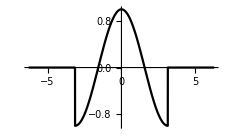

В Wolfram Mathematica существует целый ряд функций для работы с преобразованием Фурье. Рассмотрим две основные функции: FourierTransform и InverseFourierTransform. Внутри системы они определены следующим образом:

FourierTransform[f(t),t,ω] :   ℱ[f]= S(ω)= √((|b|)/(2π)^(1-a))∫_(-∞)^∞ f(t) e^(i b ω t)dt.

InverseFourierTransform[S(ω),ω,t] :  ℱ^-1[f]=  f(t)= √((|b|)/(2π)^(1+a))∫_(-∞)^∞ F(ω) e^-ibωt dω.

где {a,b} - параметры Фурье (FourierParameters).

В соответствии с данным нами определением отображения Фурье (17) параметры {a,b} = {0,-1}. Однако, по умолчанию в системе Mathematica {a,b}={0,1}. Для того чтобы изменить их стандартное значение, воспользуемся функцией SetOptions:

```mathematica
SetOptions[FourierTransform,FourierParameters-> {0,-1}];
SetOptions[InverseFourierTransform, FourierParameters-> {0,-1}];
```

Итак, для того чтобы найти спектральную плотность заданной функции f(t), воспользуемся опцией FouirierTransform:

```mathematica
Evaluate@FourierTransform[f[t],t,w,Assumptions-> a>0]
```

(√(2/π) w Sin[(π w)/a])/(a^2-w^2)

Такой же результат мы получим, интегрируя функцию по формуле (17):

```mathematica
Integrate[1/(√(2Pi))f[t] Exp[- I w t],{t,-Infinity,Infinity},Assumptions->a>0]
```

-(√(2/π) w Sin[(π w)/a])/(-a^2+w^2)

Получили следующий результат:

ℱ[f]=S(ω)=(√(2/π) ω Sin[(π ω)/a])/(a^2-ω^2)

Значит теперь можно представить исходную функцию в виде:

f(t)=1/(√(2π))∫_(-∞)^∞ (√(2/π) ω Sin[(π ω)/a])/(a^2-ω^2)ⅇ^(ⅈ ω t)ⅆω=1/π∫_(-∞)^∞ (ω Sin[(π ω)/a])/(a^2-ω^2)ⅇ^(ⅈ ω t)ⅆω

##### Пример №12.517

Найти пару косинус- или синус- преобразований указанной функции:

f(t)=1/(a^2+t^2),a>0.

Так как данная функция четная, воспользуемся формулой (19), для того чтобы найти косинус-преобразование исходной функции:

```mathematica
Integrate[√(2/Pi)1/(a^2+t^2)Cos[w t],{t,0,Infinity},Assumptions->a>0]
```

ConditionalExpression[(ⅇ^(-a Abs[w]) √(π/2))/a,w∈Reals]

При условии, что ω принадлежит множеству действительных чисел, получили:

f^*(ω)=√(π/2)ⅇ^(-a |ω|)/a

Тогда заданную функцию можно записать в виде:

f(t)=1/a∫_0^∞ ⅇ^(-a ω)cos(ω t)ⅆω

Разумеется, Wolfram Mathematica предоставляет удобные опции FourierCosTransform и FourierSinTransform для нахождения косинус- и синус преобразований Фурье.

##### Пример №12.518

Найти пару косинус- или синус- преобразований указанной функции:

f(t)=t/(a^2+t^2),a>0.

Так как исходная функция нечетная, воспользуемся функцией FourierSinTransofrm:

```mathematica
FourierSinTransform[t/(a^2+t^2),t,w,Assumptions->a>0]
```

ⅇ^(-a w) √(π/2)

Получили, что:

f_*(ω)=ⅇ^(-a ω) √(π/2)
f(t)=∫_0^∞ ⅇ^(-a ω)sin(ω t)ⅆω

### 7.6. Свойства преобразования Фурье

Пусть функциям f(t), g(t) соответствуют преобразования Фурье F(ω),G(ω). Тогда запишем основные свойства Фурье-преобразования (без доказательств):

1. Линейность

ℱ[a f(t)+b g(t)]=a F(ω)+b G(ω)

2. Запаздывание

ℱ[f(t-a)]=ⅇ^(-ⅈ ω a)F(ω)

3. Частотный сдвиг

ℱ[ⅇ^(- ⅈ a t)f(t)]=F(ω-a)

4. Масштабирование

ℱ[f(a t)]=1/(|a|)F(ω/a)

5. Преобразование Фурье n-ой производной

ℱ[ⅆ^n/(ⅆ t^n)f(t)]=(ⅈ ω)^n F(ω)

6. Дифференцирование изображения

ℱ[t^n f(t)]=ⅈ^n ⅆ^n/(ⅆ ω^n)F(ω)

7. Преобразование свертки

ℱ[(f*g)(t)]=√(2π)F(ω)G(ω)

8. Преобразование произведения

ℱ[f(t)g(t)]=1/(√(2π))(F*G)(ω)

9. Преобразование дельта-функции Дирака

ℱ[δ(t)]=1/(√(2π))

10. Преобразование константы

ℱ[a]=a √(2π)δ(t)

11. Преобразование многочленов:

ℱ[t^n]=ⅈ^n √(2π)δ^(n)(ω)
где n- натуральное число, δ^(n)(ω)- n-я обобщенная производная дельта-функции.

12. Изображения некоторых функций:

ℱ[ⅇ^(- ⅈ a t)]=√(2π)δ(ω-a)

ℱ[cos(a t)]=√(2π)(δ(ω-a)+δ(ω+a))/2

ℱ[sin(a t)]=√(2π)(δ(ω-a)-δ(ω+a))/(2ⅈ)

ℱ[ⅇ^(- a t^2)]=1/(√(2a))ⅇ^(-ω^2/4a)

ℱ[ⅇ^(- t^2/2)]=ⅇ^(-ω^2/2) -  функция Гаусса совпадает со своим изображением

ℱ[1/t]=-ⅈ √(π/2)sign(ω)

ℱ[1/t^n]=-ⅈ √(π/2)(-ⅈ ω)^(n-1)/((n-1)!)sign(ω)

ℱ[sign(t)]=√(2/π)(- ⅈ ω)^-1

ℱ[√(2π)H(t)]=1/(ⅈ ω)+π δ(ω)
H(t)- функция Хевисайда.

Рассмотрим несколько тривиальных примеров применения данных свойств.

##### Пример №1

Найти изображение многочлена:

P_5(t)=24 t^5-3 t^4+11 t^2-t+2

Применив свойства 1 и 11, получаем следующий результат:

ℱ[24 t^5-3 t^4+11 t^2-t+2]=24ℱ[t^5]-3ℱ[t^4]+11ℱ[t^2]-ℱ[t]+2ℱ[1]=
=√(2π)(24 ⅈ^5 δ^(5)(ω)-3 ⅈ^4 δ^(4)(ω)-11 ⅈ^2 δ''(ω)-ⅈδ'(ω)+2δ(ω))=
=√(2π)(24ⅈ δ^(5)(ω)-3δ^(4)(ω)+11δ''(ω)-ⅈ δ'(ω)+2δ(ω))

Тот же результат получим при помощи FourierTransform:

```mathematica
FourierTransform[24 t^5-3 t^4+11 t^2-t+2,t,w]//TraditionalForm
```

2 √(2 π) w-ⅈ √(2 π) δ'(w)-11 √(2 π) δ''(w)-3 √(2 π) δ^(4)(w)+24 ⅈ √(2 π) δ^(5)(w)

##### Пример №2

Найти изображение дифференциального выражения:

x''+2x'+x=sin(t)

Обозначим ℱ[x(t)]=X(ω).Тогда согласно свойству 5 имеем:

ℱ[x''+2x'+x-ⅇ^-t]=ℱ[x'']+2ℱ[x']+ℱ[x]-ℱ[sin(t)]=
=(ⅈ ω)^2 X+2(i ω)X+X-√(2π)(δ(ω-1)-δ(ω+1))/(2ⅈ)

Отсюда видно, что:

- ω^2X+2i ω X+X=√(2π)(δ(ω-1)-δ(ω+1))/(2ⅈ)
X=√(2π)(δ(ω-1)-δ(ω+1))/(2ⅈ)
X(ω)=√(2π)(δ(ω-1)-δ(ω+1))/(2ⅈ(-ω^2+2i ω+1))

Найдем функцию x(t):

```mathematica
InverseFourierTransform[√(2π)(DiracDelta[(ω-1)]-DiracDelta[(ω+1)])/(2I(-ω^2+2I ω+1)),ω,t]
```

-Cos[t]/2

Получается, что частное решение исходного дифференциального уравнения:

x(t)=-1/2cos(t)

##### Пример №3

Зная изображение функции f(t), найти изображение функции g(t):

ℱ[1/(a^2+t^2)]=√(π/2)ⅇ^(-a ω)/a,g(t)=t^4/(a^2+t^2)

Согласно свойству 6 имеем:

t^4/(a^2+t^2)=t^4 f(t),    ℱ[t^4 f(t)]=ⅈ^4 ⅆ^4/(ⅆ ω^4)ℱ[f(t)]
ℱ[t^4/(a^2+t^2)]=√(π/2)ⅆ^4/(ⅆ ω^4)(ⅇ^(-a ω)/a)

Найдем производную 4-ого порядка:

```mathematica
D[Exp[-a w]/a,{w,4}]
```

a^3 ⅇ^(-a w)

В итоге, получаем ответ:

ℱ[t^4/(a^2+t^2)]=√(π/2)a^3 ⅇ^(-a ω)

### 7.7. Связь коэффициентов ряда Фурье с коэффициентами ряда Лорана.

Пусть функция f(z) регулярна в кольце r_1< |z|<1+r_2 (0≤ r_1<1, r_2>0) содержащем единичную окружность |z|=1. Тогда она представляется в этом кольце рядом Лорана:

f(z)=∑_(n=-∞)^∞ c_n z^n

Откуда, полагая z=ⅇ^(i ϕ), получаем разложения в ряд Фурье функции:

F(ϕ)=f(ⅇ^iϕ)=∑_(n=-∞)^∞ c_n ⅇ^(ⅈ ϕ n)

Отсюда следует обратное: если функция F(ϕ) представляется в виде: F(ϕ)=f(ⅇ^(ⅈ ϕ)) , где функция f(z) регулярна в кольце, то ряд (43) является рядом Фурье для F(ϕ).

##### Пример №12.352

Найти все разложения указанных функций в ряды Лорана по степеням z-z_0.

f(z)=1/(z(z-1)),z_0=1

Запишем функцию:

```mathematica
f[z_]:=1/(z(z-1))
```

Как уже можно было заметить, Mathematica не предоставляет встроенных средств для разложения функций в ряд Лорана. В ней есть только функция Series, которая находит разложение в ряд лишь в окрестности точки z_0.

Однако, благодаря связи ряда Лорана и Фурье, а также тому, что Mathematica имеет целый ряд функций для работы с рядами Фурье, можно составить алгоритм разложения функции в ряд Лорана через ряд Фурье.

Изобразим особые точки функции f(z), выберем контур С, составим множество коэффициентов ряда Фурье для этого контура, и затем сформируем из них ряд Лорана.

```mathematica
Graphics[{Circle[{1,0},1/2],Circle[{1,0},3/2],Text["r_1",{1/2,1/2}],Text["r_2",{3/2,3/2}],PointSize[Large],Point[ReIm[z/.Solve[f[z]^-1==0,z]]]},PlotRange->{{-3,3},{-3,3}},Frame->False,Axes->True,AxesLabel->{Re,Im}]
```

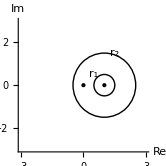

Найдем коэффициенты ряда Лорана при 0< |z-1|<1 . Для этого выберем контур r_1 и воспользуемся функцией FourierCoefficient.

Выберем, к примеру, r_1=1/2. Тогда получим замену: z-z_0=r ⅇ^(ⅈ t), z=z_0+r ⅇ^(ⅈ t)

```mathematica
Table[FourierCoefficient[f[1+1/2 Exp[I t]],t,n]/(1/2)^n,{n,1,10}]
```

{1,-1,1,-1,1,-1,1,-1,1,-1}

Примечание: действие деления на r^n следует из следующего: заменив z=r ⅇ^(ⅈ t) получаем, что f(r ⅇ^(ⅈ t))=∑_(-∞)^∞ c_n r^n ⅇ^(ⅈ n t), тогда, чтобы получить c_n- коэффициент Лорана, необходимо разделить получившийся коэффициент Фурье на r^n.

Составим ряд Лорана вида:

f(z)=∑_(n=-k)^k (c_n(z-z_0))^n

```mathematica
lor[z_,k_,r_]:=Sum[Evaluate[FourierCoefficient[f[1+r Exp[I t]],t,n]]/(r)^n (z-1)^n,{n,-k,k}]
```

```mathematica
lor[z,8,1/2]
```

-2+1/(-1+z)-(-1+z)^2+(-1+z)^3-(-1+z)^4+(-1+z)^5-(-1+z)^6+(-1+z)^7-(-1+z)^8+z

Теперь можно найти разложение функции в кольце |z-1| >1:

```mathematica
lor[z,8,3]
```

1/(-1+z)^8-1/(-1+z)^7+1/(-1+z)^6-1/(-1+z)^5+1/(-1+z)^4-1/(-1+z)^3+1/(-1+z)^2

Сравним получившиеся ответы с тем, что получается при использовании функции loranO (из Главы 2 Параграфа 5):

```mathematica
loranO[z,1/(z(z-1)),1,1/2,8]
loranO[z,1/(z(z-1)),1,3,8]
```

-2+1/(-1+z)-(-1+z)^2+(-1+z)^3-(-1+z)^4+(-1+z)^5-(-1+z)^6+(-1+z)^7-(-1+z)^8+z

1/(-1+z)^8-1/(-1+z)^7+1/(-1+z)^6-1/(-1+z)^5+1/(-1+z)^4-1/(-1+z)^3+1/(-1+z)^2

Получили такие же ответы.

##### Программный модуль

Опыт, полученный в предыдущем примере, используем для составления программного модуля:

```mathematica
loranFC[expr_,{z_,z0_,k_},r_]:=Module[{c},
c[n_]:=FourierCoefficient[expr/.z->z0+r Exp[I t],t,n]/(r)^n;
Sum[c[n](z-z0)^n,{n,-k,k}]]
```

Продемонстрируем пример:

```mathematica
loranFC[1/(z(z-1)),{z,1,8},3]
```

1/(-1+z)^8-1/(-1+z)^7+1/(-1+z)^6-1/(-1+z)^5+1/(-1+z)^4-1/(-1+z)^3+1/(-1+z)^2

Сравним время работы получившегося алгоритма и алгоритма, работающего на основе вычетов (из Главы 2 Параграфа 6):

```mathematica
t1=Timing[loranFC[1/(z(z-1)),{z,1,8},3]]
t2=Timing[loranR[1/(z(z-1)),{z,1,8},3]]
```

{17.4063,1/(-1+z)^8-1/(-1+z)^7+1/(-1+z)^6-1/(-1+z)^5+1/(-1+z)^4-1/(-1+z)^3+1/(-1+z)^2}

{0.03125,1/(-1+z)^8-1/(-1+z)^7+1/(-1+z)^6-1/(-1+z)^5+1/(-1+z)^4-1/(-1+z)^3+1/(-1+z)^2}

```mathematica
t1[[1]]/t2[[1]]
```

557.

Как мы видим, алгоритм на основе вычетов работает почти в 600 раз быстрее. Поэтому в дальнейшем использовать  метод на основе ряда Фурье для разложения функций в ряд Лорана не будем.

### 7.8. Ядро Дирихле. Интеграл Дирихле.

Введем обозначения: A_n(x)=a_n cos(n x)+b_n sin(n x), где a_n,b_n- коэффициенты Фурье

A_n(x)=a_n cos(n x)+b_n sin(n x),где a_n,b_n- коэффициенты Фурье
S_n(x)=∑_(k=0)^n A_k(x) -частичные суммы ряда Фурье
σ(x)=∑_(k=0)^∞ A_k(x)- ряд Фурье

Запишем частичную сумму ряда:

S_n(x)=∑_(k=0)^n A_k(x) =1/(2π)∫_-π^π f(t)ⅆt+∑_(k=1)^n (1/π∫_-π^π f(t)cos (k t)ⅆt cos (k x)+1/π∫_-π^π f(t)sin (k t)ⅆt sin (k x))

По свойствам интеграла, внося знак суммы под знак интеграла, получаем:

S_n(x)=∫_-π^π f(t)1/π(1/2+∑_(k=1)^n (cos (k t) cos (k x)+sin (k t)sin (k x)))ⅆt=∫_-π^π f(t)1/π(1/2+∑_(k=1)^n cos (k (t-x)))ⅆt

Тригонометрический полином вида:

D_n(t)=1/π(1/2+∑_(k=1)^n cos (k t))

называется ядром Дирихле.

Подставляя эту функцию в формулу для частичной суммы, получаем следующее выражение:

S_n(x)=∫_-π^π f(t)D_n(t-x)ⅆt

которое называется интегралом Дирихле.

##### Пример

Найдем выражение для ядра:

```mathematica
1/Pi(1/2+Sum[Cos[k t],{k,1,n}])//FullSimplify
```

(Csc[t/2] Sin[(1/2+n) t])/(2 π)

Получили, что:

D_n(t)=1/π(1/2+∑_(k=1)^n cos (k t))=1/(2π)(sin( (1/2+n) t))/(sin(t/2))